```mathematica
(*反時計まわりが正か負か，人によってことなる．
反時計回りが正のことが多いようなので，ここでもそのように決める*)
Clear["Global`*"];
```

```mathematica
(*(*回転について*)
Rx[t_]:={{1,0,0},{0,Cos[t],Sin[t]},{0,-Sin[t],Cos[t]}}
Ry[t_]:={{Cos[t],0,-Sin[t]},{0,1,0},{Sin[t],0,Cos[t]}}
Rz[t_]:={{Cos[t],-Sin[t],0},{Sin[t],Cos[t],0},{0,0,1}}*)
```

```mathematica
(*(*z->x->zオイラー角*)
Dot[Rz[t3],Dot[Rx[t2],Rz[t1]]]//MatrixForm
(*ヨー->ピッチ->ロール角*)
Dot[Rx[t3],Dot[Ry[t2],Rz[t1]]]//MatrixForm*)
```

```mathematica
(*(*オイラー角*)
Dot[Rz[γ],Dot[Rx[β],Rz[α]]]//MatrixForm
(*ヨーピッチロール角*)
Dot[Rx[ϕ],Dot[Ry[θ],Rz[ψ]]]//MatrixForm*)
```

### 回転行列

```mathematica
Clear["Global`*"];
Rs[{a_,b_,c_,d_}]:=Module[{ind,s,a2,b2,c2,d2},
a2=a*a;
b2=b*b;
c2=c*c;
d2=d*d;
(*s=1/(a*a+b*b+c*c+d*d);*)
(*{{-2*s*(c2+d2),
2*s*(b*c-d*a),
2*s*(b*d+c*a)},
{2*s*(b*c+d*a),
-2*s*(b2+d2),
2*s*(c*d-b*a)},
{2*s*(b*d-c*a),
2*s*(c*d+b*a),
-2*s*(b2+c2)}}*)
s=1;
(*{{-2*s*(c2+d2),
2*s*(b*c-d*a),
2*s*(b*d+c*a)},
{2*s*(b*c+d*a),
-2*s*(b2+d2),
2*s*(c*d-b*a)},
{2*s*(b*d-c*a),
2*s*(c*d+b*a),
-2*s*(b2+c2)}}*)
(*{{a2+b2-c2-d2,2*b*c-2a*d,2b*d+2a*c},
{2b*c+2a*d,a2-b2+c2-d2,2c*d-2a*b},
{2b*d-2a*c,2c*d+2a*b,a2-b2-c2+d2}}*)
{{a2+b2-c2-d2,2*b*c+2*a*d,-2*a*c+2*b*d},
{2*b*c-2*a*d,a2-b2+c2-d2,2*a*b+2*c*d},
{2*a*c+2*b*d,-2*a*b+2*c*d,a2-b2-c2+d2}}
];
Rv[{a_,b_,c_,d_}]=Inverse@Rs[{a,b,c,d}];

AxisAngleToQuaternion[{axX_,axY_,axZ_},angle_]:=Module[{n},
n=Normalize[{axX,axY,axZ}];
Return[{Cos[-angle/2],n[[1]]*Sin[-angle/2],n[[2]]*Sin[-angle/2],n[[3]]*Sin[-angle/2]}];
]
(*IDEN ={{1,0,0},{0,1,0},{0,0,1}};
S[{a_,b_,c_,d_}]:=1/Sqrt[(a*a+b*b+c*c+d*d)];
R[{a_,b_,c_,d_}]:=IDEN+R0[{a,b,c,d}]*S[{a,b,c,d}];*)
rep={a^2->a2,b^2->b2,d^2->d2,c^2->c2,
a^3->a3,b^3->b3,d^3->d3,c^3->c2,
(a2 + b2 + c2 + d2)->a2b2c2d2,
u0^2->u02,u1^2->u12,u2^2->u22,u3^2->u32,u4^2->u42,u5^2->u52,gx0^2+gy0^2+gz0^2+mx0^2+my0^2+mz0^2->normGM2,Power->pow};

R[{a_,b_,c_,d_}]:=Rs[{a,b,c,d}];


Print["空間を回転させる回転行列"]
Print[CForm[Rs[{a,b,c,d}]/.rep]]
Print["空間を固定しベクトルを回転させる回転行列"]
Print[CForm[Transpose[Rs[{a,b,c,d}]/.rep]]]
N@R[Normalize@{4,1,2,3}]

Tmag = {{Tmag00,Tmag01,Tmag02},
{Tmag10,Tmag11,Tmag12},
{Tmag20,Tmag21,Tmag22}};

RR[{a_,b_,c_,d_}]:=Module[{zeros,r},
zeros=Table[Table[0,{i,0,2,1}],{j,0,2,1}];
r=Rs[{a,b,c,d}];(*ベクトルを回転する行列*)
Join[Join[r,zeros,2],Join[zeros,Dot[r,Tmag],2]]
]
```

空間を回転させる回転行列

List(List(a2 + b2 - c2 - d2,2*b*c + 2*a*d,-2*a*c + 2*b*d),List(2*b*c - 2*a*d,a2 - b2 + c2 - d2,2*a*b + 2*c*d),List(2*a*c + 2*b*d,-2*a*b + 2*c*d,a2 - b2 - c2 + d2))

空間を固定しベクトルを回転させる回転行列

List(List(a2 + b2 - c2 - d2,2*b*c - 2*a*d,2*a*c + 2*b*d),List(2*b*c + 2*a*d,a2 - b2 + c2 - d2,-2*a*b + 2*c*d),List(-2*a*c + 2*b*d,2*a*b + 2*c*d,a2 - b2 - c2 + d2))

{{0.133333,0.933333,-0.333333},{-0.666667,0.333333,0.666667},{0.733333,0.133333,0.666667}}

```mathematica
(*磁場センサーのキャリブレーション*)
(*InitM= {InitMx,InitMy,InitMz}*)
{bx,by,bz}={1.22,1.32,0.62}
{Mx0,My0,Mz0}={-11.54,-12.3,-8.2}
{Mx1,My1,Mz1}={-11.8,-12.6,-4.1}
{Mx2,My2,Mz2}={-14.6,-8.1,-4.8}

InitM={Mx0,My0,Mz0}; {InitMx,InitMy,InitMz}

InvRs0=Inverse@Rs[AxisAngleToQuaternion[{1,1,1},0/180*Pi]]
InvRs1=Inverse@Rs[AxisAngleToQuaternion[{1,1,1},120/180*Pi]]
InvRs2=Inverse@Rs[AxisAngleToQuaternion[{1,1,1},240/180*Pi]]


Mb[{Mx_,My_,Mz_}]:={{Mx-bx,My-by,Mz-bz,0,0,0,0,0,0},
{0,0,0,Mx-bx,My-by,Mz-bz,0,0,0},
{0,0,0,0,0,0,Mx-bx,My-by,Mz-bz}}

MatrxMb=Join[Mb[{Mx0,My0,Mz0}],
Mb[{Mx1,My1,Mz1}],
Mb[{Mx2,My2,Mz2}]]

RsInitM=Join[Dot[InvRs0,InitM],
Dot[InvRs1,InitM],
Dot[InvRs2,InitM]]

FullSimplify@Dot[Inverse[MatrxMb],RsInitM]
```

{1.22,1.32,0.62}

{-11.54,-12.3,-8.2}

{-11.8,-12.6,-4.1}

{-14.6,-8.1,-4.8}

{InitMx,InitMy,InitMz}

{{1,0,0},{0,1,0},{0,0,1}}

{{0,1,0},{0,0,1},{1,0,0}}

{{0,0,1},{1,0,0},{0,1,0}}

{{-12.76,-13.62,-8.82,0,0,0,0,0,0},{0,0,0,-12.76,-13.62,-8.82,0,0,0},{0,0,0,0,0,0,-12.76,-13.62,-8.82},{-13.02,-13.92,-4.72,0,0,0,0,0,0},{0,0,0,-13.02,-13.92,-4.72,0,0,0},{0,0,0,0,0,0,-13.02,-13.92,-4.72},{-15.82,-9.42,-5.42,0,0,0,0,0,0},{0,0,0,-15.82,-9.42,-5.42,0,0,0},{0,0,0,0,0,0,-15.82,-9.42,-5.42}}

{-11.54,-12.3,-8.2,-12.3,-8.2,-11.54,-8.2,-11.54,-12.3}

{0.0197872,0.905085,-0.117885,0.532323,-0.253073,1.01524,0.875692,0.260873,-0.740014}

### 姿勢の計算１：物体の加速度を無視し，重力加速度だけがかかっているとして，物体の姿勢を計測する方法

```mathematica
(*満たすべき方程式*)
Q=Table[q[i],{i,0,3,1}];
{v0[0],v0[1],v0[2],v0[3],v0[4],v0[5]}={gx0,gy0,gz0,mx0,my0,mz0};(*物体の加速度を無視し，重力加速度だけがかかっている．実際は{gx0,gy0,gz0}に物体の加速度がかかっている*)
{u[0],u[1],u[2],u[3],u[4],u[5]}={Ax,Ay,Az,Mx,My,Mz};(*sensor value*)


Print["RR(q)=RR({a,b,c,d})=",RR[{a,b,c,d}]//MatrixForm]
(*関数*)

originalEq[{a_,b_,c_,d_}]=Module[{},
Table[(u[i]-Sum[RR[{a,b,c,d}][[i+1]][[j+1]]*v0[j],{j,0,5,1}])^2,{i,0,5,1}]
];
CForm[FullSimplify[originalEq[{a,b,c,d}]]]/.rep/.rep/.Power->pow



f[{a_,b_,c_,d_}]=Sum[(u[i]-Sum[RR[{a,b,c,d}][[i+1]][[j+1]]*v0[j],{j,0,5,1}])^2,{i,0,5,1}]/4(*+(1-Sqrt[a^2+b^2+c^2+d^2])*);
Print[CForm[(Simplify@f[{a,b,c,d}])/.rep/.rep]/.Power->pow]
(*最小にする関数の微分*)
F[{a_,b_,c_,d_}]=Simplify@{
D[f[{A,b,c,d}],A]/.{A->a},
D[f[{a,B,c,d}],B]/.{B->b},
D[f[{a,b,C,d}],C]/.{C->c},
D[f[{a,b,c,dd}],dd]/.{dd->d}
};
(*最小にする関数の微分の微分*)
DF[{a_,b_,c_,d_}]=Simplify[{
D[F[{A,b,c,d}],A]/.{A->a},
D[F[{a,B,c,d}],B]/.{B->b},
D[F[{a,b,C,d}],C]/.{C->c},
D[F[{a,b,c,dd}],dd]/.{dd->d}}]
```

RR(q)=RR({a,b,c,d})=(a^2+b^2-c^2-d^2 | 2 b c+2 a d | -2 a c+2 b d | 0 | 0 | 0
2 b c-2 a d | a^2-b^2+c^2-d^2 | 2 a b+2 c d | 0 | 0 | 0
2 a c+2 b d | -2 a b+2 c d | a^2-b^2-c^2+d^2 | 0 | 0 | 0
0 | 0 | 0 | (a^2+b^2-c^2-d^2) Tmag00+(2 b c+2 a d) Tmag10+(-2 a c+2 b d) Tmag20 | (a^2+b^2-c^2-d^2) Tmag01+(2 b c+2 a d) Tmag11+(-2 a c+2 b d) Tmag21 | (a^2+b^2-c^2-d^2) Tmag02+(2 b c+2 a d) Tmag12+(-2 a c+2 b d) Tmag22
0 | 0 | 0 | (2 b c-2 a d) Tmag00+(a^2-b^2+c^2-d^2) Tmag10+(2 a b+2 c d) Tmag20 | (2 b c-2 a d) Tmag01+(a^2-b^2+c^2-d^2) Tmag11+(2 a b+2 c d) Tmag21 | (2 b c-2 a d) Tmag02+(a^2-b^2+c^2-d^2) Tmag12+(2 a b+2 c d) Tmag22
0 | 0 | 0 | (2 a c+2 b d) Tmag00+(-2 a b+2 c d) Tmag10+(a^2-b^2-c^2+d^2) Tmag20 | (2 a c+2 b d) Tmag01+(-2 a b+2 c d) Tmag11+(a^2-b^2-c^2+d^2) Tmag21 | (2 a c+2 b d) Tmag02+(-2 a b+2 c d) Tmag12+(a^2-b^2-c^2+d^2) Tmag22)

(pow(Ax - a2*gx0 - b2*gx0 + c2*gx0 + d2*gx0 - 2*b*c*gy0 - 2*a*d*gy0 + 2*a*c*gz0 - 2*b*d*gz0,2) + pow(Az - 2*a*c*gx0 - 2*b*d*gx0 + 2*a*b*gy0 - 2*c*d*gy0 - a2*gz0 + b2*gz0 + c2*gz0 - d2*gz0,2) + pow(Ay + 2*a*d*gx0 - a2*gy0 + b2*gy0 - c2*gy0 + d2*gy0 - 2*c*d*gz0 - 2*b*(c*gx0 + a*gz0),2) + pow(-My + mx0*(2*(b*c - a*d)*Tmag00 + (a2 - b2 + c2 - d2)*Tmag10 + 2*(a*b + c*d)*Tmag20) + my0*(2*(b*c - a*d)*Tmag01 + (a2 - b2 + c2 - d2)*Tmag11 + 2*(a*b + c*d)*Tmag21) + mz0*(2*(b*c - a*d)*Tmag02 + (a2 - b2 + c2 - d2)*Tmag12 + 2*(a*b + c*d)*Tmag22),2) + pow(-Mz + mx0*(2*(a*c + b*d)*Tmag00 + (-2*a*b + 2*c*d)*Tmag10 + (a2 - b2 - c2 + d2)*Tmag20) + my0*(2*(a*c + b*d)*Tmag01 + (-2*a*b + 2*c*d)*Tmag11 + (a2 - b2 - c2 + d2)*Tmag21) + mz0*(2*(a*c + b*d)*Tmag02 + (-2*a*b + 2*c*d)*Tmag12 + (a2 - b2 - c2 + d2)*Tmag22),2) + pow(-Mx + mx0*(a2*Tmag00 + b2*Tmag00 - (c2 + d2)*Tmag00 + 2*a*(d*Tmag10 - c*Tmag20) + 2*b*(c*Tmag10 + d*Tmag20)) + my0*(a2*Tmag01 + b2*Tmag01 - (c2 + d2)*Tmag01 + 2*a*(d*Tmag11 - c*Tmag21) + 2*b*(c*Tmag11 + d*Tmag21)) + mz0*(a2*Tmag02 + b2*Tmag02 - (c2 + d2)*Tmag02 + 2*a*(d*Tmag12 - c*Tmag22) + 2*b*(c*Tmag12 + d*Tmag22)),2))/4.

{{-Ax gx0+b^2 gx0^2+c^2 gx0^2+d^2 gx0^2-Ay gy0+b^2 gy0^2+c^2 gy0^2+d^2 gy0^2-Az gz0+b^2 gz0^2+c^2 gz0^2+d^2 gz0^2-Mx mx0 Tmag00+b^2 mx0^2 Tmag00^2+c^2 mx0^2 Tmag00^2+d^2 mx0^2 Tmag00^2-Mx my0 Tmag01+2 b^2 mx0 my0 Tmag00 Tmag01+2 c^2 mx0 my0 Tmag00 Tmag01+2 d^2 mx0 my0 Tmag00 Tmag01+b^2 my0^2 Tmag01^2+c^2 my0^2 Tmag01^2+d^2 my0^2 Tmag01^2-Mx mz0 Tmag02+2 b^2 mx0 mz0 Tmag00 Tmag02+2 c^2 mx0 mz0 Tmag00 Tmag02+2 d^2 mx0 mz0 Tmag00 Tmag02+2 b^2 my0 mz0 Tmag01 Tmag02+2 c^2 my0 mz0 Tmag01 Tmag02+2 d^2 my0 mz0 Tmag01 Tmag02+b^2 mz0^2 Tmag02^2+c^2 mz0^2 Tmag02^2+d^2 mz0^2 Tmag02^2-mx0 My Tmag10+b^2 mx0^2 Tmag10^2+c^2 mx0^2 Tmag10^2+d^2 mx0^2 Tmag10^2-My my0 Tmag11+2 b^2 mx0 my0 Tmag10 Tmag11+2 c^2 mx0 my0 Tmag10 Tmag11+2 d^2 mx0 my0 Tmag10 Tmag11+b^2 my0^2 Tmag11^2+c^2 my0^2 Tmag11^2+d^2 my0^2 Tmag11^2-My mz0 Tmag12+2 b^2 mx0 mz0 Tmag10 Tmag12+2 c^2 mx0 mz0 Tmag10 Tmag12+2 d^2 mx0 mz0 Tmag10 Tmag12+2 b^2 my0 mz0 Tmag11 Tmag12+2 c^2 my0 mz0 Tmag11 Tmag12+2 d^2 my0 mz0 Tmag11 Tmag12+b^2 mz0^2 Tmag12^2+c^2 mz0^2 Tmag12^2+d^2 mz0^2 Tmag12^2-mx0 Mz Tmag20+b^2 mx0^2 Tmag20^2+c^2 mx0^2 Tmag20^2+d^2 mx0^2 Tmag20^2-my0 Mz Tmag21+2 b^2 mx0 my0 Tmag20 Tmag21+2 c^2 mx0 my0 Tmag20 Tmag21+2 d^2 mx0 my0 Tmag20 Tmag21+b^2 my0^2 Tmag21^2+c^2 my0^2 Tmag21^2+d^2 my0^2 Tmag21^2-Mz mz0 Tmag22+2 b^2 mx0 mz0 Tmag20 Tmag22+2 c^2 mx0 mz0 Tmag20 Tmag22+2 d^2 mx0 mz0 Tmag20 Tmag22+2 b^2 my0 mz0 Tmag21 Tmag22+2 c^2 my0 mz0 Tmag21 Tmag22+2 d^2 my0 mz0 Tmag21 Tmag22+b^2 mz0^2 Tmag22^2+c^2 mz0^2 Tmag22^2+d^2 mz0^2 Tmag22^2+3 a^2 (gx0^2+gy0^2+gz0^2+mx0^2 Tmag00^2+2 mx0 my0 Tmag00 Tmag01+my0^2 Tmag01^2+2 mx0 mz0 Tmag00 Tmag02+2 my0 mz0 Tmag01 Tmag02+mz0^2 Tmag02^2+mx0^2 Tmag10^2+2 mx0 my0 Tmag10 Tmag11+my0^2 Tmag11^2+2 mx0 mz0 Tmag10 Tmag12+2 my0 mz0 Tmag11 Tmag12+mz0^2 Tmag12^2+mx0^2 Tmag20^2+2 mx0 my0 Tmag20 Tmag21+my0^2 Tmag21^2+2 mx0 mz0 Tmag20 Tmag22+2 my0 mz0 Tmag21 Tmag22+mz0^2 Tmag22^2),Az gy0-Ay gz0+mx0 Mz Tmag10+my0 Mz Tmag11+Mz mz0 Tmag12-mx0 My Tmag20-My my0 Tmag21-My mz0 Tmag22+2 a b (gx0^2+gy0^2+gz0^2+mx0^2 Tmag00^2+2 mx0 my0 Tmag00 Tmag01+my0^2 Tmag01^2+2 mx0 mz0 Tmag00 Tmag02+2 my0 mz0 Tmag01 Tmag02+mz0^2 Tmag02^2+mx0^2 Tmag10^2+2 mx0 my0 Tmag10 Tmag11+my0^2 Tmag11^2+2 mx0 mz0 Tmag10 Tmag12+2 my0 mz0 Tmag11 Tmag12+mz0^2 Tmag12^2+mx0^2 Tmag20^2+2 mx0 my0 Tmag20 Tmag21+my0^2 Tmag21^2+2 mx0 mz0 Tmag20 Tmag22+2 my0 mz0 Tmag21 Tmag22+mz0^2 Tmag22^2),-Az gx0+Ax gz0-mx0 Mz Tmag00-my0 Mz Tmag01-Mz mz0 Tmag02+Mx mx0 Tmag20+Mx my0 Tmag21+Mx mz0 Tmag22+2 a c (gx0^2+gy0^2+gz0^2+mx0^2 Tmag00^2+2 mx0 my0 Tmag00 Tmag01+my0^2 Tmag01^2+2 mx0 mz0 Tmag00 Tmag02+2 my0 mz0 Tmag01 Tmag02+mz0^2 Tmag02^2+mx0^2 Tmag10^2+2 mx0 my0 Tmag10 Tmag11+my0^2 Tmag11^2+2 mx0 mz0 Tmag10 Tmag12+2 my0 mz0 Tmag11 Tmag12+mz0^2 Tmag12^2+mx0^2 Tmag20^2+2 mx0 my0 Tmag20 Tmag21+my0^2 Tmag21^2+2 mx0 mz0 Tmag20 Tmag22+2 my0 mz0 Tmag21 Tmag22+mz0^2 Tmag22^2),Ay gx0-Ax gy0+mx0 My Tmag00+My my0 Tmag01+My mz0 Tmag02-Mx mx0 Tmag10-Mx my0 Tmag11-Mx mz0 Tmag12+2 a d (gx0^2+gy0^2+gz0^2+mx0^2 Tmag00^2+2 mx0 my0 Tmag00 Tmag01+my0^2 Tmag01^2+2 mx0 mz0 Tmag00 Tmag02+2 my0 mz0 Tmag01 Tmag02+mz0^2 Tmag02^2+mx0^2 Tmag10^2+2 mx0 my0 Tmag10 Tmag11+my0^2 Tmag11^2+2 mx0 mz0 Tmag10 Tmag12+2 my0 mz0 Tmag11 Tmag12+mz0^2 Tmag12^2+mx0^2 Tmag20^2+2 mx0 my0 Tmag20 Tmag21+my0^2 Tmag21^2+2 mx0 mz0 Tmag20 Tmag22+2 my0 mz0 Tmag21 Tmag22+mz0^2 Tmag22^2)},{Az gy0-Ay gz0+mx0 Mz Tmag10+my0 Mz Tmag11+Mz mz0 Tmag12-mx0 My Tmag20-My my0 Tmag21-My mz0 Tmag22+2 a b (gx0^2+gy0^2+gz0^2+mx0^2 Tmag00^2+2 mx0 my0 Tmag00 Tmag01+my0^2 Tmag01^2+2 mx0 mz0 Tmag00 Tmag02+2 my0 mz0 Tmag01 Tmag02+mz0^2 Tmag02^2+mx0^2 Tmag10^2+2 mx0 my0 Tmag10 Tmag11+my0^2 Tmag11^2+2 mx0 mz0 Tmag10 Tmag12+2 my0 mz0 Tmag11 Tmag12+mz0^2 Tmag12^2+mx0^2 Tmag20^2+2 mx0 my0 Tmag20 Tmag21+my0^2 Tmag21^2+2 mx0 mz0 Tmag20 Tmag22+2 my0 mz0 Tmag21 Tmag22+mz0^2 Tmag22^2),-Ax gx0+3 b^2 gx0^2+c^2 gx0^2+d^2 gx0^2+Ay gy0+3 b^2 gy0^2+c^2 gy0^2+d^2 gy0^2+Az gz0+3 b^2 gz0^2+c^2 gz0^2+d^2 gz0^2-Mx mx0 Tmag00+3 b^2 mx0^2 Tmag00^2+c^2 mx0^2 Tmag00^2+d^2 mx0^2 Tmag00^2-Mx my0 Tmag01+6 b^2 mx0 my0 Tmag00 Tmag01+2 c^2 mx0 my0 Tmag00 Tmag01+2 d^2 mx0 my0 Tmag00 Tmag01+3 b^2 my0^2 Tmag01^2+c^2 my0^2 Tmag01^2+d^2 my0^2 Tmag01^2-Mx mz0 Tmag02+6 b^2 mx0 mz0 Tmag00 Tmag02+2 c^2 mx0 mz0 Tmag00 Tmag02+2 d^2 mx0 mz0 Tmag00 Tmag02+6 b^2 my0 mz0 Tmag01 Tmag02+2 c^2 my0 mz0 Tmag01 Tmag02+2 d^2 my0 mz0 Tmag01 Tmag02+3 b^2 mz0^2 Tmag02^2+c^2 mz0^2 Tmag02^2+d^2 mz0^2 Tmag02^2+mx0 My Tmag10+3 b^2 mx0^2 Tmag10^2+c^2 mx0^2 Tmag10^2+d^2 mx0^2 Tmag10^2+My my0 Tmag11+6 b^2 mx0 my0 Tmag10 Tmag11+2 c^2 mx0 my0 Tmag10 Tmag11+2 d^2 mx0 my0 Tmag10 Tmag11+3 b^2 my0^2 Tmag11^2+c^2 my0^2 Tmag11^2+d^2 my0^2 Tmag11^2+My mz0 Tmag12+6 b^2 mx0 mz0 Tmag10 Tmag12+2 c^2 mx0 mz0 Tmag10 Tmag12+2 d^2 mx0 mz0 Tmag10 Tmag12+6 b^2 my0 mz0 Tmag11 Tmag12+2 c^2 my0 mz0 Tmag11 Tmag12+2 d^2 my0 mz0 Tmag11 Tmag12+3 b^2 mz0^2 Tmag12^2+c^2 mz0^2 Tmag12^2+d^2 mz0^2 Tmag12^2+mx0 Mz Tmag20+3 b^2 mx0^2 Tmag20^2+c^2 mx0^2 Tmag20^2+d^2 mx0^2 Tmag20^2+my0 Mz Tmag21+6 b^2 mx0 my0 Tmag20 Tmag21+2 c^2 mx0 my0 Tmag20 Tmag21+2 d^2 mx0 my0 Tmag20 Tmag21+3 b^2 my0^2 Tmag21^2+c^2 my0^2 Tmag21^2+d^2 my0^2 Tmag21^2+Mz mz0 Tmag22+6 b^2 mx0 mz0 Tmag20 Tmag22+2 c^2 mx0 mz0 Tmag20 Tmag22+2 d^2 mx0 mz0 Tmag20 Tmag22+6 b^2 my0 mz0 Tmag21 Tmag22+2 c^2 my0 mz0 Tmag21 Tmag22+2 d^2 my0 mz0 Tmag21 Tmag22+3 b^2 mz0^2 Tmag22^2+c^2 mz0^2 Tmag22^2+d^2 mz0^2 Tmag22^2+a^2 (gx0^2+gy0^2+gz0^2+mx0^2 Tmag00^2+2 mx0 my0 Tmag00 Tmag01+my0^2 Tmag01^2+2 mx0 mz0 Tmag00 Tmag02+2 my0 mz0 Tmag01 Tmag02+mz0^2 Tmag02^2+mx0^2 Tmag10^2+2 mx0 my0 Tmag10 Tmag11+my0^2 Tmag11^2+2 mx0 mz0 Tmag10 Tmag12+2 my0 mz0 Tmag11 Tmag12+mz0^2 Tmag12^2+mx0^2 Tmag20^2+2 mx0 my0 Tmag20 Tmag21+my0^2 Tmag21^2+2 mx0 mz0 Tmag20 Tmag22+2 my0 mz0 Tmag21 Tmag22+mz0^2 Tmag22^2),-Ay gx0-Ax gy0-mx0 My Tmag00-My my0 Tmag01-My mz0 Tmag02-Mx mx0 Tmag10-Mx my0 Tmag11-Mx mz0 Tmag12+2 b c (gx0^2+gy0^2+gz0^2+mx0^2 Tmag00^2+2 mx0 my0 Tmag00 Tmag01+my0^2 Tmag01^2+2 mx0 mz0 Tmag00 Tmag02+2 my0 mz0 Tmag01 Tmag02+mz0^2 Tmag02^2+mx0^2 Tmag10^2+2 mx0 my0 Tmag10 Tmag11+my0^2 Tmag11^2+2 mx0 mz0 Tmag10 Tmag12+2 my0 mz0 Tmag11 Tmag12+mz0^2 Tmag12^2+mx0^2 Tmag20^2+2 mx0 my0 Tmag20 Tmag21+my0^2 Tmag21^2+2 mx0 mz0 Tmag20 Tmag22+2 my0 mz0 Tmag21 Tmag22+mz0^2 Tmag22^2),-Az gx0-Ax gz0-mx0 Mz Tmag00-my0 Mz Tmag01-Mz mz0 Tmag02-Mx mx0 Tmag20-Mx my0 Tmag21-Mx mz0 Tmag22+2 b d (gx0^2+gy0^2+gz0^2+mx0^2 Tmag00^2+2 mx0 my0 Tmag00 Tmag01+my0^2 Tmag01^2+2 mx0 mz0 Tmag00 Tmag02+2 my0 mz0 Tmag01 Tmag02+mz0^2 Tmag02^2+mx0^2 Tmag10^2+2 mx0 my0 Tmag10 Tmag11+my0^2 Tmag11^2+2 mx0 mz0 Tmag10 Tmag12+2 my0 mz0 Tmag11 Tmag12+mz0^2 Tmag12^2+mx0^2 Tmag20^2+2 mx0 my0 Tmag20 Tmag21+my0^2 Tmag21^2+2 mx0 mz0 Tmag20 Tmag22+2 my0 mz0 Tmag21 Tmag22+mz0^2 Tmag22^2)},{-Az gx0+Ax gz0-mx0 Mz Tmag00-my0 Mz Tmag01-Mz mz0 Tmag02+Mx mx0 Tmag20+Mx my0 Tmag21+Mx mz0 Tmag22+2 a c (gx0^2+gy0^2+gz0^2+mx0^2 Tmag00^2+2 mx0 my0 Tmag00 Tmag01+my0^2 Tmag01^2+2 mx0 mz0 Tmag00 Tmag02+2 my0 mz0 Tmag01 Tmag02+mz0^2 Tmag02^2+mx0^2 Tmag10^2+2 mx0 my0 Tmag10 Tmag11+my0^2 Tmag11^2+2 mx0 mz0 Tmag10 Tmag12+2 my0 mz0 Tmag11 Tmag12+mz0^2 Tmag12^2+mx0^2 Tmag20^2+2 mx0 my0 Tmag20 Tmag21+my0^2 Tmag21^2+2 mx0 mz0 Tmag20 Tmag22+2 my0 mz0 Tmag21 Tmag22+mz0^2 Tmag22^2),-Ay gx0-Ax gy0-mx0 My Tmag00-My my0 Tmag01-My mz0 Tmag02-Mx mx0 Tmag10-Mx my0 Tmag11-Mx mz0 Tmag12+2 b c (gx0^2+gy0^2+gz0^2+mx0^2 Tmag00^2+2 mx0 my0 Tmag00 Tmag01+my0^2 Tmag01^2+2 mx0 mz0 Tmag00 Tmag02+2 my0 mz0 Tmag01 Tmag02+mz0^2 Tmag02^2+mx0^2 Tmag10^2+2 mx0 my0 Tmag10 Tmag11+my0^2 Tmag11^2+2 mx0 mz0 Tmag10 Tmag12+2 my0 mz0 Tmag11 Tmag12+mz0^2 Tmag12^2+mx0^2 Tmag20^2+2 mx0 my0 Tmag20 Tmag21+my0^2 Tmag21^2+2 mx0 mz0 Tmag20 Tmag22+2 my0 mz0 Tmag21 Tmag22+mz0^2 Tmag22^2),Ax gx0+b^2 gx0^2+3 c^2 gx0^2+d^2 gx0^2-Ay gy0+b^2 gy0^2+3 c^2 gy0^2+d^2 gy0^2+Az gz0+b^2 gz0^2+3 c^2 gz0^2+d^2 gz0^2+Mx mx0 Tmag00+b^2 mx0^2 Tmag00^2+3 c^2 mx0^2 Tmag00^2+d^2 mx0^2 Tmag00^2+Mx my0 Tmag01+2 b^2 mx0 my0 Tmag00 Tmag01+6 c^2 mx0 my0 Tmag00 Tmag01+2 d^2 mx0 my0 Tmag00 Tmag01+b^2 my0^2 Tmag01^2+3 c^2 my0^2 Tmag01^2+d^2 my0^2 Tmag01^2+Mx mz0 Tmag02+2 b^2 mx0 mz0 Tmag00 Tmag02+6 c^2 mx0 mz0 Tmag00 Tmag02+2 d^2 mx0 mz0 Tmag00 Tmag02+2 b^2 my0 mz0 Tmag01 Tmag02+6 c^2 my0 mz0 Tmag01 Tmag02+2 d^2 my0 mz0 Tmag01 Tmag02+b^2 mz0^2 Tmag02^2+3 c^2 mz0^2 Tmag02^2+d^2 mz0^2 Tmag02^2-mx0 My Tmag10+b^2 mx0^2 Tmag10^2+3 c^2 mx0^2 Tmag10^2+d^2 mx0^2 Tmag10^2-My my0 Tmag11+2 b^2 mx0 my0 Tmag10 Tmag11+6 c^2 mx0 my0 Tmag10 Tmag11+2 d^2 mx0 my0 Tmag10 Tmag11+b^2 my0^2 Tmag11^2+3 c^2 my0^2 Tmag11^2+d^2 my0^2 Tmag11^2-My mz0 Tmag12+2 b^2 mx0 mz0 Tmag10 Tmag12+6 c^2 mx0 mz0 Tmag10 Tmag12+2 d^2 mx0 mz0 Tmag10 Tmag12+2 b^2 my0 mz0 Tmag11 Tmag12+6 c^2 my0 mz0 Tmag11 Tmag12+2 d^2 my0 mz0 Tmag11 Tmag12+b^2 mz0^2 Tmag12^2+3 c^2 mz0^2 Tmag12^2+d^2 mz0^2 Tmag12^2+mx0 Mz Tmag20+b^2 mx0^2 Tmag20^2+3 c^2 mx0^2 Tmag20^2+d^2 mx0^2 Tmag20^2+my0 Mz Tmag21+2 b^2 mx0 my0 Tmag20 Tmag21+6 c^2 mx0 my0 Tmag20 Tmag21+2 d^2 mx0 my0 Tmag20 Tmag21+b^2 my0^2 Tmag21^2+3 c^2 my0^2 Tmag21^2+d^2 my0^2 Tmag21^2+Mz mz0 Tmag22+2 b^2 mx0 mz0 Tmag20 Tmag22+6 c^2 mx0 mz0 Tmag20 Tmag22+2 d^2 mx0 mz0 Tmag20 Tmag22+2 b^2 my0 mz0 Tmag21 Tmag22+6 c^2 my0 mz0 Tmag21 Tmag22+2 d^2 my0 mz0 Tmag21 Tmag22+b^2 mz0^2 Tmag22^2+3 c^2 mz0^2 Tmag22^2+d^2 mz0^2 Tmag22^2+a^2 (gx0^2+gy0^2+gz0^2+mx0^2 Tmag00^2+2 mx0 my0 Tmag00 Tmag01+my0^2 Tmag01^2+2 mx0 mz0 Tmag00 Tmag02+2 my0 mz0 Tmag01 Tmag02+mz0^2 Tmag02^2+mx0^2 Tmag10^2+2 mx0 my0 Tmag10 Tmag11+my0^2 Tmag11^2+2 mx0 mz0 Tmag10 Tmag12+2 my0 mz0 Tmag11 Tmag12+mz0^2 Tmag12^2+mx0^2 Tmag20^2+2 mx0 my0 Tmag20 Tmag21+my0^2 Tmag21^2+2 mx0 mz0 Tmag20 Tmag22+2 my0 mz0 Tmag21 Tmag22+mz0^2 Tmag22^2),-Az gy0-Ay gz0-mx0 Mz Tmag10-my0 Mz Tmag11-Mz mz0 Tmag12-mx0 My Tmag20-My my0 Tmag21-My mz0 Tmag22+2 c d (gx0^2+gy0^2+gz0^2+mx0^2 Tmag00^2+2 mx0 my0 Tmag00 Tmag01+my0^2 Tmag01^2+2 mx0 mz0 Tmag00 Tmag02+2 my0 mz0 Tmag01 Tmag02+mz0^2 Tmag02^2+mx0^2 Tmag10^2+2 mx0 my0 Tmag10 Tmag11+my0^2 Tmag11^2+2 mx0 mz0 Tmag10 Tmag12+2 my0 mz0 Tmag11 Tmag12+mz0^2 Tmag12^2+mx0^2 Tmag20^2+2 mx0 my0 Tmag20 Tmag21+my0^2 Tmag21^2+2 mx0 mz0 Tmag20 Tmag22+2 my0 mz0 Tmag21 Tmag22+mz0^2 Tmag22^2)},{Ay gx0-Ax gy0+mx0 My Tmag00+My my0 Tmag01+My mz0 Tmag02-Mx mx0 Tmag10-Mx my0 Tmag11-Mx mz0 Tmag12+2 a d (gx0^2+gy0^2+gz0^2+mx0^2 Tmag00^2+2 mx0 my0 Tmag00 Tmag01+my0^2 Tmag01^2+2 mx0 mz0 Tmag00 Tmag02+2 my0 mz0 Tmag01 Tmag02+mz0^2 Tmag02^2+mx0^2 Tmag10^2+2 mx0 my0 Tmag10 Tmag11+my0^2 Tmag11^2+2 mx0 mz0 Tmag10 Tmag12+2 my0 mz0 Tmag11 Tmag12+mz0^2 Tmag12^2+mx0^2 Tmag20^2+2 mx0 my0 Tmag20 Tmag21+my0^2 Tmag21^2+2 mx0 mz0 Tmag20 Tmag22+2 my0 mz0 Tmag21 Tmag22+mz0^2 Tmag22^2),-Az gx0-Ax gz0-mx0 Mz Tmag00-my0 Mz Tmag01-Mz mz0 Tmag02-Mx mx0 Tmag20-Mx my0 Tmag21-Mx mz0 Tmag22+2 b d (gx0^2+gy0^2+gz0^2+mx0^2 Tmag00^2+2 mx0 my0 Tmag00 Tmag01+my0^2 Tmag01^2+2 mx0 mz0 Tmag00 Tmag02+2 my0 mz0 Tmag01 Tmag02+mz0^2 Tmag02^2+mx0^2 Tmag10^2+2 mx0 my0 Tmag10 Tmag11+my0^2 Tmag11^2+2 mx0 mz0 Tmag10 Tmag12+2 my0 mz0 Tmag11 Tmag12+mz0^2 Tmag12^2+mx0^2 Tmag20^2+2 mx0 my0 Tmag20 Tmag21+my0^2 Tmag21^2+2 mx0 mz0 Tmag20 Tmag22+2 my0 mz0 Tmag21 Tmag22+mz0^2 Tmag22^2),-Az gy0-Ay gz0-mx0 Mz Tmag10-my0 Mz Tmag11-Mz mz0 Tmag12-mx0 My Tmag20-My my0 Tmag21-My mz0 Tmag22+2 c d (gx0^2+gy0^2+gz0^2+mx0^2 Tmag00^2+2 mx0 my0 Tmag00 Tmag01+my0^2 Tmag01^2+2 mx0 mz0 Tmag00 Tmag02+2 my0 mz0 Tmag01 Tmag02+mz0^2 Tmag02^2+mx0^2 Tmag10^2+2 mx0 my0 Tmag10 Tmag11+my0^2 Tmag11^2+2 mx0 mz0 Tmag10 Tmag12+2 my0 mz0 Tmag11 Tmag12+mz0^2 Tmag12^2+mx0^2 Tmag20^2+2 mx0 my0 Tmag20 Tmag21+my0^2 Tmag21^2+2 mx0 mz0 Tmag20 Tmag22+2 my0 mz0 Tmag21 Tmag22+mz0^2 Tmag22^2),Ax gx0+b^2 gx0^2+c^2 gx0^2+3 d^2 gx0^2+Ay gy0+b^2 gy0^2+c^2 gy0^2+3 d^2 gy0^2-Az gz0+b^2 gz0^2+c^2 gz0^2+3 d^2 gz0^2+Mx mx0 Tmag00+b^2 mx0^2 Tmag00^2+c^2 mx0^2 Tmag00^2+3 d^2 mx0^2 Tmag00^2+Mx my0 Tmag01+2 b^2 mx0 my0 Tmag00 Tmag01+2 c^2 mx0 my0 Tmag00 Tmag01+6 d^2 mx0 my0 Tmag00 Tmag01+b^2 my0^2 Tmag01^2+c^2 my0^2 Tmag01^2+3 d^2 my0^2 Tmag01^2+Mx mz0 Tmag02+2 b^2 mx0 mz0 Tmag00 Tmag02+2 c^2 mx0 mz0 Tmag00 Tmag02+6 d^2 mx0 mz0 Tmag00 Tmag02+2 b^2 my0 mz0 Tmag01 Tmag02+2 c^2 my0 mz0 Tmag01 Tmag02+6 d^2 my0 mz0 Tmag01 Tmag02+b^2 mz0^2 Tmag02^2+c^2 mz0^2 Tmag02^2+3 d^2 mz0^2 Tmag02^2+mx0 My Tmag10+b^2 mx0^2 Tmag10^2+c^2 mx0^2 Tmag10^2+3 d^2 mx0^2 Tmag10^2+My my0 Tmag11+2 b^2 mx0 my0 Tmag10 Tmag11+2 c^2 mx0 my0 Tmag10 Tmag11+6 d^2 mx0 my0 Tmag10 Tmag11+b^2 my0^2 Tmag11^2+c^2 my0^2 Tmag11^2+3 d^2 my0^2 Tmag11^2+My mz0 Tmag12+2 b^2 mx0 mz0 Tmag10 Tmag12+2 c^2 mx0 mz0 Tmag10 Tmag12+6 d^2 mx0 mz0 Tmag10 Tmag12+2 b^2 my0 mz0 Tmag11 Tmag12+2 c^2 my0 mz0 Tmag11 Tmag12+6 d^2 my0 mz0 Tmag11 Tmag12+b^2 mz0^2 Tmag12^2+c^2 mz0^2 Tmag12^2+3 d^2 mz0^2 Tmag12^2-mx0 Mz Tmag20+b^2 mx0^2 Tmag20^2+c^2 mx0^2 Tmag20^2+3 d^2 mx0^2 Tmag20^2-my0 Mz Tmag21+2 b^2 mx0 my0 Tmag20 Tmag21+2 c^2 mx0 my0 Tmag20 Tmag21+6 d^2 mx0 my0 Tmag20 Tmag21+b^2 my0^2 Tmag21^2+c^2 my0^2 Tmag21^2+3 d^2 my0^2 Tmag21^2-Mz mz0 Tmag22+2 b^2 mx0 mz0 Tmag20 Tmag22+2 c^2 mx0 mz0 Tmag20 Tmag22+6 d^2 mx0 mz0 Tmag20 Tmag22+2 b^2 my0 mz0 Tmag21 Tmag22+2 c^2 my0 mz0 Tmag21 Tmag22+6 d^2 my0 mz0 Tmag21 Tmag22+b^2 mz0^2 Tmag22^2+c^2 mz0^2 Tmag22^2+3 d^2 mz0^2 Tmag22^2+a^2 (gx0^2+gy0^2+gz0^2+mx0^2 Tmag00^2+2 mx0 my0 Tmag00 Tmag01+my0^2 Tmag01^2+2 mx0 mz0 Tmag00 Tmag02+2 my0 mz0 Tmag01 Tmag02+mz0^2 Tmag02^2+mx0^2 Tmag10^2+2 mx0 my0 Tmag10 Tmag11+my0^2 Tmag11^2+2 mx0 mz0 Tmag10 Tmag12+2 my0 mz0 Tmag11 Tmag12+mz0^2 Tmag12^2+mx0^2 Tmag20^2+2 mx0 my0 Tmag20 Tmag21+my0^2 Tmag21^2+2 mx0 mz0 Tmag20 Tmag22+2 my0 mz0 Tmag21 Tmag22+mz0^2 Tmag22^2)}}

List(pow(Ax - a2*gx0 - b2*gx0 + (c2 + d2)*gx0 + a*(-2*d*gy0 + 2*c*gz0) - 2*b*(c*gy0 + d*gz0),2),
   pow(Ay + 2*a*d*gx0 - a2*gy0 + b2*gy0 - c2*gy0 + d2*gy0 - 2*c*d*gz0 - 2*b*(c*gx0 + a*gz0),2),
   pow(Az - 2*(a*c*gx0 + b*d*gx0 - a*b*gy0 + c*d*gy0) + (-a2 + b2 + c2 - d2)*gz0,2),
   pow(Mx - a2*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02) - b2*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02) + (c2 + d2)*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02) - 
     2*a*d*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) + 2*a*c*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22) - 
     2*b*(c*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) + d*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22)),2),
   pow(My + 2*a*d*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02) - c2*mx0*Tmag10 + d2*mx0*Tmag10 - c2*my0*Tmag11 + d2*my0*Tmag11 - c2*mz0*Tmag12 + d2*mz0*Tmag12 - 
     a2*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) + b2*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) - 2*c*d*mx0*Tmag20 - 2*c*d*my0*Tmag21 - 2*c*d*mz0*Tmag22 - 
     2*b*(c*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02) + a*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22)),2),
   pow(-Mz + 2*mx0*(a*c*Tmag00 + b*d*Tmag00 - a*b*Tmag10 + c*d*Tmag10) + 2*my0*(a*c*Tmag01 + b*d*Tmag01 - a*b*Tmag11 + c*d*Tmag11) + 
     2*mz0*(a*c*Tmag02 + b*d*Tmag02 - a*b*Tmag12 + c*d*Tmag12) + (a2 - b2 - c2 + d2)*mx0*Tmag20 + (a2 - b2 - c2 + d2)*my0*Tmag21 + (a2 - b2 - c2 + d2)*mz0*Tmag22,2))

```mathematica
(*確認*)
Print["Rs = ",CForm[R[{a,b,c,d}]/.rep]]

tmp=Collect[F[{a,b,c,d}],Table[u[i],{i,0,5,1}],FullSimplify]/.rep/.rep/.rep(*/.{gx0->0,gy0->0,gz0->-1}*);
Print["変数",Variables@tmp]
Print["=",Table[CForm[tmp[[i]]],{i,1,Length[tmp],1}]]

tmp=Collect[DF[{a,b,c,d}],Table[u[i],{i,0,5,1}],FullSimplify]/.rep/.rep(*/.{gx0->0,gy0->0,gz0->-1}*);
Print["変数",Variables@tmp]
Do[Print@CForm[FullSimplify[tmp[[i]]]],{i,1,Length[tmp],1}]
```

Rs = List(List(a2 + b2 - c2 - d2,2*b*c + 2*a*d,-2*a*c + 2*b*d),List(2*b*c - 2*a*d,a2 - b2 + c2 - d2,2*a*b + 2*c*d),List(2*a*c + 2*b*d,-2*a*b + 2*c*d,a2 - b2 - c2 + d2))

変数{a,a2b2c2d2,Ax,Ay,Az,b,c,d,gx0,gy0,gz0,Mx,mx0,My,my0,Mz,mz0,Tmag00,Tmag01,Tmag02,Tmag10,Tmag11,Tmag12,Tmag20,Tmag21,Tmag22,pow[gx0,2],pow[gy0,2],pow[gz0,2],pow[mx0,2],pow[my0,2],pow[mz0,2],pow[Tmag00,2],pow[Tmag01,2],pow[Tmag02,2],pow[Tmag10,2],pow[Tmag11,2],pow[Tmag12,2],pow[Tmag20,2],pow[Tmag21,2],pow[Tmag22,2]}

={Az*(-(c*gx0) + b*gy0 - a*gz0) + Ay*(d*gx0 - a*gy0 - b*gz0) + Ax*(-(a*gx0) - d*gy0 + c*gz0) + Mz*(-(c*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02)) + b*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) - a*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22)) + My*(d*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02) - a*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) - b*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22)) + Mx*(-(a*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02)) - d*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) + c*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22)) + a*a2b2c2d2*(2*my0*mz0*(Tmag01*Tmag02 + Tmag11*Tmag12 + Tmag21*Tmag22) + 2*mx0*(my0*(Tmag00*Tmag01 + Tmag10*Tmag11 + Tmag20*Tmag21) + mz0*(Tmag00*Tmag02 + Tmag10*Tmag12 + Tmag20*Tmag22)) + pow(gx0,2) + pow(gy0,2) + pow(gz0,2) + pow(mx0,2)*(pow(Tmag00,2) + pow(Tmag10,2) + pow(Tmag20,2)) + pow(my0,2)*(pow(Tmag01,2) + pow(Tmag11,2) + pow(Tmag21,2)) + pow(mz0,2)*(pow(Tmag02,2) + pow(Tmag12,2) + pow(Tmag22,2))),Ay*(-(c*gx0) + b*gy0 - a*gz0) + Az*(-(d*gx0) + a*gy0 + b*gz0) + Ax*(-(b*gx0) - c*gy0 - d*gz0) + My*(-(c*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02)) + b*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) - a*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22)) + Mz*(-(d*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02)) + a*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) + b*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22)) + Mx*(-(b*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02)) - c*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) - d*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22)) + a2b2c2d2*b*(2*my0*mz0*(Tmag01*Tmag02 + Tmag11*Tmag12 + Tmag21*Tmag22) + 2*mx0*(my0*(Tmag00*Tmag01 + Tmag10*Tmag11 + Tmag20*Tmag21) + mz0*(Tmag00*Tmag02 + Tmag10*Tmag12 + Tmag20*Tmag22)) + pow(gx0,2) + pow(gy0,2) + pow(gz0,2) + pow(mx0,2)*(pow(Tmag00,2) + pow(Tmag10,2) + pow(Tmag20,2)) + pow(my0,2)*(pow(Tmag01,2) + pow(Tmag11,2) + pow(Tmag21,2)) + pow(mz0,2)*(pow(Tmag02,2) + pow(Tmag12,2) + pow(Tmag22,2))),Ax*(c*gx0 - b*gy0 + a*gz0) + Az*(-(a*gx0) - d*gy0 + c*gz0) + Ay*(-(b*gx0) - c*gy0 - d*gz0) + Mx*(c*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02) - b*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) + a*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22)) + Mz*(-(a*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02)) - d*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) + c*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22)) + My*(-(b*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02)) - c*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) - d*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22)) + a2b2c2d2*c*(2*my0*mz0*(Tmag01*Tmag02 + Tmag11*Tmag12 + Tmag21*Tmag22) + 2*mx0*(my0*(Tmag00*Tmag01 + Tmag10*Tmag11 + Tmag20*Tmag21) + mz0*(Tmag00*Tmag02 + Tmag10*Tmag12 + Tmag20*Tmag22)) + pow(gx0,2) + pow(gy0,2) + pow(gz0,2) + pow(mx0,2)*(pow(Tmag00,2) + pow(Tmag10,2) + pow(Tmag20,2)) + pow(my0,2)*(pow(Tmag01,2) + pow(Tmag11,2) + pow(Tmag21,2)) + pow(mz0,2)*(pow(Tmag02,2) + pow(Tmag12,2) + pow(Tmag22,2))),Ax*(d*gx0 - a*gy0 - b*gz0) + Ay*(a*gx0 + d*gy0 - c*gz0) + Az*(-(b*gx0) - c*gy0 - d*gz0) + Mx*(d*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02) - a*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) - b*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22)) + My*(a*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02) + d*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) - c*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22)) + Mz*(-(b*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02)) - c*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) - d*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22)) + a2b2c2d2*d*(2*my0*mz0*(Tmag01*Tmag02 + Tmag11*Tmag12 + Tmag21*Tmag22) + 2*mx0*(my0*(Tmag00*Tmag01 + Tmag10*Tmag11 + Tmag20*Tmag21) + mz0*(Tmag00*Tmag02 + Tmag10*Tmag12 + Tmag20*Tmag22)) + pow(gx0,2) + pow(gy0,2) + pow(gz0,2) + pow(mx0,2)*(pow(Tmag00,2) + pow(Tmag10,2) + pow(Tmag20,2)) + pow(my0,2)*(pow(Tmag01,2) + pow(Tmag11,2) + pow(Tmag21,2)) + pow(mz0,2)*(pow(Tmag02,2) + pow(Tmag12,2) + pow(Tmag22,2)))}

変数{a,a2,Ax,Ay,Az,b,b2,c,c2,d,d2,gx0,gy0,gz0,Mx,mx0,My,my0,Mz,mz0,Tmag00,Tmag01,Tmag02,Tmag10,Tmag11,Tmag12,Tmag20,Tmag21,Tmag22,pow[gx0,2],pow[gy0,2],pow[gz0,2],pow[mx0,2],pow[my0,2],pow[mz0,2],pow[Tmag00,2],pow[Tmag01,2],pow[Tmag02,2],pow[Tmag10,2],pow[Tmag11,2],pow[Tmag12,2],pow[Tmag20,2],pow[Tmag21,2],pow[Tmag22,2]}

List(-(Ax*gx0) - Ay*gy0 - Az*gz0 - Mx*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02) - My*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) - Mz*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22) + (3*a2 + b2 + c2 + d2)*(2*my0*mz0*(Tmag01*Tmag02 + Tmag11*Tmag12 + Tmag21*Tmag22) + 2*mx0*(my0*(Tmag00*Tmag01 + Tmag10*Tmag11 + Tmag20*Tmag21) + mz0*(Tmag00*Tmag02 + Tmag10*Tmag12 + Tmag20*Tmag22)) + pow(gx0,2) + pow(gy0,2) + pow(gz0,2) + pow(mx0,2)*(pow(Tmag00,2) + pow(Tmag10,2) + pow(Tmag20,2)) + pow(my0,2)*(pow(Tmag01,2) + pow(Tmag11,2) + pow(Tmag21,2)) + pow(mz0,2)*(pow(Tmag02,2) + pow(Tmag12,2) + pow(Tmag22,2))),Az*gy0 - Ay*gz0 + Mz*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) - My*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22) + 2*a*b*(2*my0*mz0*(Tmag01*Tmag02 + Tmag11*Tmag12 + Tmag21*Tmag22) + 2*mx0*(my0*(Tmag00*Tmag01 + Tmag10*Tmag11 + Tmag20*Tmag21) + mz0*(Tmag00*Tmag02 + Tmag10*Tmag12 + Tmag20*Tmag22)) + pow(gx0,2) + pow(gy0,2) + pow(gz0,2) + pow(mx0,2)*(pow(Tmag00,2) + pow(Tmag10,2) + pow(Tmag20,2)) + pow(my0,2)*(pow(Tmag01,2) + pow(Tmag11,2) + pow(Tmag21,2)) + pow(mz0,2)*(pow(Tmag02,2) + pow(Tmag12,2) + pow(Tmag22,2))),-(Az*gx0) + Ax*gz0 - Mz*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02) + Mx*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22) + 2*a*c*(2*my0*mz0*(Tmag01*Tmag02 + Tmag11*Tmag12 + Tmag21*Tmag22) + 2*mx0*(my0*(Tmag00*Tmag01 + Tmag10*Tmag11 + Tmag20*Tmag21) + mz0*(Tmag00*Tmag02 + Tmag10*Tmag12 + Tmag20*Tmag22)) + pow(gx0,2) + pow(gy0,2) + pow(gz0,2) + pow(mx0,2)*(pow(Tmag00,2) + pow(Tmag10,2) + pow(Tmag20,2)) + pow(my0,2)*(pow(Tmag01,2) + pow(Tmag11,2) + pow(Tmag21,2)) + pow(mz0,2)*(pow(Tmag02,2) + pow(Tmag12,2) + pow(Tmag22,2))),Ay*gx0 - Ax*gy0 + My*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02) - Mx*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) + 2*a*d*(2*my0*mz0*(Tmag01*Tmag02 + Tmag11*Tmag12 + Tmag21*Tmag22) + 2*mx0*(my0*(Tmag00*Tmag01 + Tmag10*Tmag11 + Tmag20*Tmag21) + mz0*(Tmag00*Tmag02 + Tmag10*Tmag12 + Tmag20*Tmag22)) + pow(gx0,2) + pow(gy0,2) + pow(gz0,2) + pow(mx0,2)*(pow(Tmag00,2) + pow(Tmag10,2) + pow(Tmag20,2)) + pow(my0,2)*(pow(Tmag01,2) + pow(Tmag11,2) + pow(Tmag21,2)) + pow(mz0,2)*(pow(Tmag02,2) + pow(Tmag12,2) + pow(Tmag22,2))))

List(Az*gy0 - Ay*gz0 + Mz*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) - My*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22) + 2*a*b*(2*my0*mz0*(Tmag01*Tmag02 + Tmag11*Tmag12 + Tmag21*Tmag22) + 2*mx0*(my0*(Tmag00*Tmag01 + Tmag10*Tmag11 + Tmag20*Tmag21) + mz0*(Tmag00*Tmag02 + Tmag10*Tmag12 + Tmag20*Tmag22)) + pow(gx0,2) + pow(gy0,2) + pow(gz0,2) + pow(mx0,2)*(pow(Tmag00,2) + pow(Tmag10,2) + pow(Tmag20,2)) + pow(my0,2)*(pow(Tmag01,2) + pow(Tmag11,2) + pow(Tmag21,2)) + pow(mz0,2)*(pow(Tmag02,2) + pow(Tmag12,2) + pow(Tmag22,2))),-(Ax*gx0) + Ay*gy0 + Az*gz0 - Mx*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02) + My*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) + Mz*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22) + (a2 + 3*b2 + c2 + d2)*(2*my0*mz0*(Tmag01*Tmag02 + Tmag11*Tmag12 + Tmag21*Tmag22) + 2*mx0*(my0*(Tmag00*Tmag01 + Tmag10*Tmag11 + Tmag20*Tmag21) + mz0*(Tmag00*Tmag02 + Tmag10*Tmag12 + Tmag20*Tmag22)) + pow(gx0,2) + pow(gy0,2) + pow(gz0,2) + pow(mx0,2)*(pow(Tmag00,2) + pow(Tmag10,2) + pow(Tmag20,2)) + pow(my0,2)*(pow(Tmag01,2) + pow(Tmag11,2) + pow(Tmag21,2)) + pow(mz0,2)*(pow(Tmag02,2) + pow(Tmag12,2) + pow(Tmag22,2))),-(Ay*gx0) - Ax*gy0 - My*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02) - Mx*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) + 2*b*c*(2*my0*mz0*(Tmag01*Tmag02 + Tmag11*Tmag12 + Tmag21*Tmag22) + 2*mx0*(my0*(Tmag00*Tmag01 + Tmag10*Tmag11 + Tmag20*Tmag21) + mz0*(Tmag00*Tmag02 + Tmag10*Tmag12 + Tmag20*Tmag22)) + pow(gx0,2) + pow(gy0,2) + pow(gz0,2) + pow(mx0,2)*(pow(Tmag00,2) + pow(Tmag10,2) + pow(Tmag20,2)) + pow(my0,2)*(pow(Tmag01,2) + pow(Tmag11,2) + pow(Tmag21,2)) + pow(mz0,2)*(pow(Tmag02,2) + pow(Tmag12,2) + pow(Tmag22,2))),-(Az*gx0) - Ax*gz0 - Mz*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02) - Mx*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22) + 2*b*d*(2*my0*mz0*(Tmag01*Tmag02 + Tmag11*Tmag12 + Tmag21*Tmag22) + 2*mx0*(my0*(Tmag00*Tmag01 + Tmag10*Tmag11 + Tmag20*Tmag21) + mz0*(Tmag00*Tmag02 + Tmag10*Tmag12 + Tmag20*Tmag22)) + pow(gx0,2) + pow(gy0,2) + pow(gz0,2) + pow(mx0,2)*(pow(Tmag00,2) + pow(Tmag10,2) + pow(Tmag20,2)) + pow(my0,2)*(pow(Tmag01,2) + pow(Tmag11,2) + pow(Tmag21,2)) + pow(mz0,2)*(pow(Tmag02,2) + pow(Tmag12,2) + pow(Tmag22,2))))

List(-(Az*gx0) + Ax*gz0 - Mz*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02) + Mx*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22) + 2*a*c*(2*my0*mz0*(Tmag01*Tmag02 + Tmag11*Tmag12 + Tmag21*Tmag22) + 2*mx0*(my0*(Tmag00*Tmag01 + Tmag10*Tmag11 + Tmag20*Tmag21) + mz0*(Tmag00*Tmag02 + Tmag10*Tmag12 + Tmag20*Tmag22)) + pow(gx0,2) + pow(gy0,2) + pow(gz0,2) + pow(mx0,2)*(pow(Tmag00,2) + pow(Tmag10,2) + pow(Tmag20,2)) + pow(my0,2)*(pow(Tmag01,2) + pow(Tmag11,2) + pow(Tmag21,2)) + pow(mz0,2)*(pow(Tmag02,2) + pow(Tmag12,2) + pow(Tmag22,2))),-(Ay*gx0) - Ax*gy0 - My*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02) - Mx*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) + 2*b*c*(2*my0*mz0*(Tmag01*Tmag02 + Tmag11*Tmag12 + Tmag21*Tmag22) + 2*mx0*(my0*(Tmag00*Tmag01 + Tmag10*Tmag11 + Tmag20*Tmag21) + mz0*(Tmag00*Tmag02 + Tmag10*Tmag12 + Tmag20*Tmag22)) + pow(gx0,2) + pow(gy0,2) + pow(gz0,2) + pow(mx0,2)*(pow(Tmag00,2) + pow(Tmag10,2) + pow(Tmag20,2)) + pow(my0,2)*(pow(Tmag01,2) + pow(Tmag11,2) + pow(Tmag21,2)) + pow(mz0,2)*(pow(Tmag02,2) + pow(Tmag12,2) + pow(Tmag22,2))),Ax*gx0 - Ay*gy0 + Az*gz0 + Mx*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02) - My*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) + Mz*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22) + (a2 + b2 + 3*c2 + d2)*(2*my0*mz0*(Tmag01*Tmag02 + Tmag11*Tmag12 + Tmag21*Tmag22) + 2*mx0*(my0*(Tmag00*Tmag01 + Tmag10*Tmag11 + Tmag20*Tmag21) + mz0*(Tmag00*Tmag02 + Tmag10*Tmag12 + Tmag20*Tmag22)) + pow(gx0,2) + pow(gy0,2) + pow(gz0,2) + pow(mx0,2)*(pow(Tmag00,2) + pow(Tmag10,2) + pow(Tmag20,2)) + pow(my0,2)*(pow(Tmag01,2) + pow(Tmag11,2) + pow(Tmag21,2)) + pow(mz0,2)*(pow(Tmag02,2) + pow(Tmag12,2) + pow(Tmag22,2))),-(Az*gy0) - Ay*gz0 - Mz*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) - My*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22) + 2*c*d*(2*my0*mz0*(Tmag01*Tmag02 + Tmag11*Tmag12 + Tmag21*Tmag22) + 2*mx0*(my0*(Tmag00*Tmag01 + Tmag10*Tmag11 + Tmag20*Tmag21) + mz0*(Tmag00*Tmag02 + Tmag10*Tmag12 + Tmag20*Tmag22)) + pow(gx0,2) + pow(gy0,2) + pow(gz0,2) + pow(mx0,2)*(pow(Tmag00,2) + pow(Tmag10,2) + pow(Tmag20,2)) + pow(my0,2)*(pow(Tmag01,2) + pow(Tmag11,2) + pow(Tmag21,2)) + pow(mz0,2)*(pow(Tmag02,2) + pow(Tmag12,2) + pow(Tmag22,2))))

List(Ay*gx0 - Ax*gy0 + My*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02) - Mx*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) + 2*a*d*(2*my0*mz0*(Tmag01*Tmag02 + Tmag11*Tmag12 + Tmag21*Tmag22) + 2*mx0*(my0*(Tmag00*Tmag01 + Tmag10*Tmag11 + Tmag20*Tmag21) + mz0*(Tmag00*Tmag02 + Tmag10*Tmag12 + Tmag20*Tmag22)) + pow(gx0,2) + pow(gy0,2) + pow(gz0,2) + pow(mx0,2)*(pow(Tmag00,2) + pow(Tmag10,2) + pow(Tmag20,2)) + pow(my0,2)*(pow(Tmag01,2) + pow(Tmag11,2) + pow(Tmag21,2)) + pow(mz0,2)*(pow(Tmag02,2) + pow(Tmag12,2) + pow(Tmag22,2))),-(Az*gx0) - Ax*gz0 - Mz*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02) - Mx*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22) + 2*b*d*(2*my0*mz0*(Tmag01*Tmag02 + Tmag11*Tmag12 + Tmag21*Tmag22) + 2*mx0*(my0*(Tmag00*Tmag01 + Tmag10*Tmag11 + Tmag20*Tmag21) + mz0*(Tmag00*Tmag02 + Tmag10*Tmag12 + Tmag20*Tmag22)) + pow(gx0,2) + pow(gy0,2) + pow(gz0,2) + pow(mx0,2)*(pow(Tmag00,2) + pow(Tmag10,2) + pow(Tmag20,2)) + pow(my0,2)*(pow(Tmag01,2) + pow(Tmag11,2) + pow(Tmag21,2)) + pow(mz0,2)*(pow(Tmag02,2) + pow(Tmag12,2) + pow(Tmag22,2))),-(Az*gy0) - Ay*gz0 - Mz*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) - My*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22) + 2*c*d*(2*my0*mz0*(Tmag01*Tmag02 + Tmag11*Tmag12 + Tmag21*Tmag22) + 2*mx0*(my0*(Tmag00*Tmag01 + Tmag10*Tmag11 + Tmag20*Tmag21) + mz0*(Tmag00*Tmag02 + Tmag10*Tmag12 + Tmag20*Tmag22)) + pow(gx0,2) + pow(gy0,2) + pow(gz0,2) + pow(mx0,2)*(pow(Tmag00,2) + pow(Tmag10,2) + pow(Tmag20,2)) + pow(my0,2)*(pow(Tmag01,2) + pow(Tmag11,2) + pow(Tmag21,2)) + pow(mz0,2)*(pow(Tmag02,2) + pow(Tmag12,2) + pow(Tmag22,2))),Ax*gx0 + Ay*gy0 - Az*gz0 + Mx*(mx0*Tmag00 + my0*Tmag01 + mz0*Tmag02) + My*(mx0*Tmag10 + my0*Tmag11 + mz0*Tmag12) - Mz*(mx0*Tmag20 + my0*Tmag21 + mz0*Tmag22) + (a2 + b2 + c2 + 3*d2)*(2*my0*mz0*(Tmag01*Tmag02 + Tmag11*Tmag12 + Tmag21*Tmag22) + 2*mx0*(my0*(Tmag00*Tmag01 + Tmag10*Tmag11 + Tmag20*Tmag21) + mz0*(Tmag00*Tmag02 + Tmag10*Tmag12 + Tmag20*Tmag22)) + pow(gx0,2) + pow(gy0,2) + pow(gz0,2) + pow(mx0,2)*(pow(Tmag00,2) + pow(Tmag10,2) + pow(Tmag20,2)) + pow(my0,2)*(pow(Tmag01,2) + pow(Tmag11,2) + pow(Tmag21,2)) + pow(mz0,2)*(pow(Tmag02,2) + pow(Tmag12,2) + pow(Tmag22,2))))

```mathematica
yaw[{a_,b_,c_,d_}]:=N@ArcTan[2*(a*d+b*c)/(1-2*(c*c+d*d))]
roll[{a_,b_,c_,d_}]:=N@ArcTan[2*(a*b+c*d)/(1-2*(b*b+c*c))]
pitch[{a_,b_,c_,d_}]:=N@ArcSin[2*(a*c-b*d)]
```

{0.201034,0.552337,-0.809017}

{Ax→0.,Ay→0.,Az→-1.,Mx→0.201034,My→0.552337,Mz→-0.809017}

Rvを使って回転させた加速度Aと磁場Mを与える．70.度となるはず

1.

{a,b,c,d}={0.819152,-8.65606×10^-18,-4.44475×10^-18,-0.573576}{0.819152,0.,0.,-0.573576}

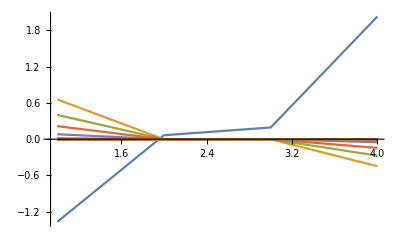

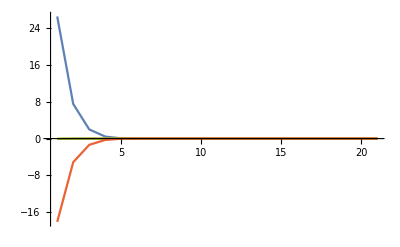

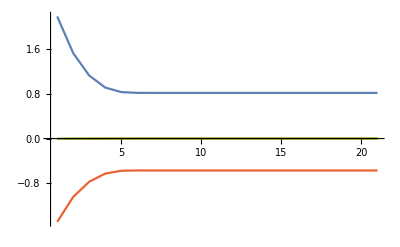

```mathematica
(*初期姿勢の静止姿勢で観測される重力加速度と磁場を設定．これはfusionの初期に一つ決める値で，DFやFに組み込まれる*)
(****************************************************)
θ=-54/180*Pi;
{gx0,gy0,gz0}={0,0,-1};(*g0*)
{mx0,my0,mz0}={Cos[θ],0,Sin[θ]};(*m0*)
(****************************************************)
(*上で設定した，初期のgとmを回転させることで，センサーの値を模擬*)
(****************************************************)
{axis,dθ}={{0,0,1},70/180.*Pi};
q=AxisAngleToQuaternion[axis,dθ];(*この回転を表すクォータニオン*)
A=Dot[Rs[q],{gx0,gy0,gz0}];(*加速度 g^*)
M=Dot[Rs[q],{mx0,my0,mz0}](*磁場 m^*)
(****************************************************)
(*模擬した値を与えて正しい結果が得られるかチェック*)
(*rep={u0->A[[1]],u1->A[[2]],u2->A[[3]],u3->M[[1]],u4->M[[2]],u5->M[[3]]}*)
rep={Ax->A[[1]],Ay->A[[2]],Az->A[[3]],Mx->M[[1]],My->M[[2]],Mz->M[[3]]}
Print["Rvを使って回転させた加速度Aと磁場Mを与える．",N[dθ]/Pi*180,"度となるはず"];

data={};
abcd={};
dq={1,0,0,0};
DQ={};

{a,b,c,d}={RandomReal[],RandomReal[],RandomReal[],RandomReal[]};
Do[
If[Mod[i,1],{a,b,c,d}=Normalize[{a,b,c,d}];];
(*{a,b,c,d}=Normalize[{a,b,c,d}];*)
dq=(Dot[Inverse[DF[{a,b,c,d}]/.rep],F[{a,b,c,d}]/.rep]);
{a,b,c,d}-=dq;
AppendTo[data,F[{a,b,c,d}]/.rep];
AppendTo[DQ,dq];
AppendTo[abcd,{a,b,c,d}/.rep];
,{i,0,20,1}];
Norm[{a,b,c,d}]
(*{a,b,c,d}=Normalize[{a,b,c,d}]*)
(*l=A*)
(*solution={Cos[θ/2.],l[[1]]*Sin[θhorion/2],l[[2]]*Sin[θhorion/2.],l[[3]]*Sin[θhorion/2.]}*)
(*Print["{Y,P,R}=",{yaw[{a,b,c,d}],roll[{a,b,c,d}],pitch[{a,b,c,d}](*,2ArcTan[Norm[{b,c,d}]/a]*)}/Pi*180]*)
Print["{a,b,c,d}=",{a,b,c,d},q]
ListPlot[DQ,Joined->True,PlotRange->All]
ListPlot[Transpose@data,Joined->True,PlotRange->All]
ListPlot[Transpose@abcd,Joined->True,PlotRange->All]
```

```mathematica
(*.08加速度をいっぺんに計算する*)
```

### 姿勢の計算２：物体の加速度を無視し，重力加速度だけがかかっているとして，物体の姿勢を計測する方法

```mathematica
(*満たすべき方程式*)
Q=Table[q[i],{i,0,3,1}];
{v0[0],v0[1],v0[2],v0[3],v0[4],v0[5],v0[6],v0[7],v0[8]}={gx0,gy0,gz0,gx0,gy0,gz0,mx0,my0,mz0};(*物体の加速度を無視し，重力加速度だけがかかっている．実際は{gx0,gy0,gz0}に物体の加速度がかかっている*)
{u[0],u[1],u[2],u[3],u[4],u[5],u[6],u[7],u[8]}={Ax,Ay,Az,Ax,Ay,Az,Mx,My,Mz};
(*sensor value*)
{U[0],U[1],U[2],U[3],U[4],U[5],U[6],U[7],U[8]}={ABODYx,ABODYy,ABODYz,ABODYx,ABODYy,ABODYz,0,0,0};
(*sensor value*)
RR[{a_,b_,c_,d_},{Aa_,Ab_,Ac_,Ad_}]:=Module[{zeros,r,approxR},
zeros=Table[Table[0,{i,0,2,1}],{j,0,2,1}];
r=Rs[{a,b,c,d}];(*ベクトルを回転する行列*)
approxR=Rs[{Aa,Ab,Ac,Ad}];
Join[
Join[approxR,zeros,zeros,2],
Join[zeros,r,zeros,2],
Join[zeros,zeros,r,2]]
];
Print["RR(q)=RR({a,b,c,d})=",RR[{a,b,c,d},{Aa,Ab,Ac,Ad}]//MatrixForm]
(*関数*)
f[{a_,b_,c_,d_},{Aa_,Ab_,Ac_,Ad_}]=Sum[(u[i]-Sum[RR[{a,b,c,d},{Aa,Ab,Ac,Ad}][[i+1]][[j+1]]*v0[j],{j,0,8,1}]-U[i])^2,{i,0,8,1}]/4(*+(1-Sqrt[a^2+b^2+c^2+d^2])*);
Print[CForm[(Simplify@f[{a,b,c,d},{Aa,Ab,Ac,Ad}])/.rep/.rep]/.Power->pow]
(*最小にする関数の微分*)
F[{a_,b_,c_,d_},{Aa_,Ab_,Ac_,Ad_}]=Simplify@{
D[f[{A,b,c,d},{Aa,Ab,Ac,Ad}],A]/.{A->a},
D[f[{a,B,c,d},{Aa,Ab,Ac,Ad}],B]/.{B->b},
D[f[{a,b,C,d},{Aa,Ab,Ac,Ad}],C]/.{C->c},
D[f[{a,b,c,dd},{Aa,Ab,Ac,Ad}],dd]/.{dd->d},
D[f[{a,b,c,d},{Aa,Ab,Ac,Ad}],ABODYx],
D[f[{a,b,c,d},{Aa,Ab,Ac,Ad}],ABODYy],
D[f[{a,b,c,d},{Aa,Ab,Ac,Ad}],ABODYz]
}
(*最小にする関数の微分の微分*)
DF[{a_,b_,c_,d_},{Aa_,Ab_,Ac_,Ad_}]=Simplify[{
D[F[{A,b,c,d},{Aa,Ab,Ac,Ad}],A]/.{A->a},
D[F[{a,B,c,d},{Aa,Ab,Ac,Ad}],B]/.{B->b},
D[F[{a,b,C,d},{Aa,Ab,Ac,Ad}],C]/.{C->c},
D[F[{a,b,c,dd},{Aa,Ab,Ac,Ad}],dd]/.{dd->d},
D[F[{a,b,c,d},{Aa,Ab,Ac,Ad}],ABODYx],
D[F[{a,b,c,d},{Aa,Ab,Ac,Ad}],ABODYy],
D[F[{a,b,c,d},{Aa,Ab,Ac,Ad}],ABODYz]}
]
```

RR(q)=RR({a,b,c,d})=(Aa^2+Ab^2-Ac^2-Ad^2 | 2 Ab Ac+2 Aa Ad | -2 Aa Ac+2 Ab Ad | 0 | 0 | 0 | 0 | 0 | 0
2 Ab Ac-2 Aa Ad | Aa^2-Ab^2+Ac^2-Ad^2 | 2 Aa Ab+2 Ac Ad | 0 | 0 | 0 | 0 | 0 | 0
2 Aa Ac+2 Ab Ad | -2 Aa Ab+2 Ac Ad | Aa^2-Ab^2-Ac^2+Ad^2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | a^2+b^2-c^2-d^2 | 2 b c+2 a d | -2 a c+2 b d | 0 | 0 | 0
0 | 0 | 0 | 2 b c-2 a d | a^2-b^2+c^2-d^2 | 2 a b+2 c d | 0 | 0 | 0
0 | 0 | 0 | 2 a c+2 b d | -2 a b+2 c d | a^2-b^2-c^2+d^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | a^2+b^2-c^2-d^2 | 2 b c+2 a d | -2 a c+2 b d
0 | 0 | 0 | 0 | 0 | 0 | 2 b c-2 a d | a^2-b^2+c^2-d^2 | 2 a b+2 c d
0 | 0 | 0 | 0 | 0 | 0 | 2 a c+2 b d | -2 a b+2 c d | a^2-b^2-c^2+d^2)

(pow(ABODYx - Ax + a2*gx0 + b2*gx0 - c2*gx0 - d2*gx0 + 2*b*c*gy0 + 2*a*d*gy0 - 2*a*c*gz0 + 2*b*d*gz0,2) + pow(ABODYy - Ay + 2*b*c*gx0 - 2*a*d*gx0 + a2*gy0 - b2*gy0 + c2*gy0 - d2*gy0 + 2*a*b*gz0 + 2*c*d*gz0,2) + pow(ABODYz - Az + 2*a*c*gx0 + 2*b*d*gx0 - 2*a*b*gy0 + 2*c*d*gy0 + a2*gz0 - b2*gz0 - c2*gz0 + d2*gz0,2) + pow(Mx - a2*mx0 - b2*mx0 + c2*mx0 + d2*mx0 - 2*b*c*my0 - 2*a*d*my0 + 2*a*c*mz0 - 2*b*d*mz0,2) + pow(-2*a*c*mx0 - 2*b*d*mx0 + 2*a*b*my0 - 2*c*d*my0 + Mz - a2*mz0 + b2*mz0 + c2*mz0 - d2*mz0,2) + pow(2*a*d*mx0 + My - a2*my0 + b2*my0 - c2*my0 + d2*my0 - 2*c*d*mz0 - 2*b*(c*mx0 + a*mz0),2) + pow(ABODYx - Ax + 2*Ab*Ac*gy0 + 2*Aa*Ad*gy0 - 2*Aa*Ac*gz0 + 2*Ab*Ad*gz0 + gx0*pow(Aa,2) + gx0*pow(Ab,2) - gx0*pow(Ac,2) - gx0*pow(Ad,2),2) + pow(ABODYy - Ay + 2*Ab*Ac*gx0 - 2*Aa*Ad*gx0 + 2*Aa*Ab*gz0 + 2*Ac*Ad*gz0 + gy0*pow(Aa,2) - gy0*pow(Ab,2) + gy0*pow(Ac,2) - gy0*pow(Ad,2),2) + pow(ABODYz - Az + 2*Aa*Ac*gx0 + 2*Ab*Ad*gx0 - 2*Aa*Ab*gy0 + 2*Ac*Ad*gy0 + gz0*pow(Aa,2) - gz0*pow(Ab,2) - gz0*pow(Ac,2) + gz0*pow(Ad,2),2))/4.

{ABODYz c gx0-Az c gx0-ABODYy d gx0+Ay d gx0-ABODYz b gy0+Az b gy0+ABODYx d gy0-Ax d gy0+ABODYy b gz0-Ay b gz0-ABODYx c gz0+Ax c gz0+d mx0 My-d Mx my0-c mx0 Mz+b my0 Mz+c Mx mz0-b My mz0+a^3 (gx0^2+gy0^2+gz0^2+mx0^2+my0^2+mz0^2)+a (ABODYx gx0-Ax gx0+b^2 gx0^2+c^2 gx0^2+d^2 gx0^2+ABODYy gy0-Ay gy0+b^2 gy0^2+c^2 gy0^2+d^2 gy0^2+ABODYz gz0-Az gz0+b^2 gz0^2+c^2 gz0^2+d^2 gz0^2-Mx mx0+b^2 mx0^2+c^2 mx0^2+d^2 mx0^2-My my0+b^2 my0^2+c^2 my0^2+d^2 my0^2-Mz mz0+b^2 mz0^2+c^2 mz0^2+d^2 mz0^2),ABODYy c gx0-Ay c gx0+ABODYz d gx0-Az d gx0+a^2 b gx0^2+b^3 gx0^2+b c^2 gx0^2+b d^2 gx0^2-a ABODYz gy0+a Az gy0-ABODYy b gy0+Ay b gy0+a^2 b gy0^2+b^3 gy0^2+b c^2 gy0^2+b d^2 gy0^2+a ABODYy gz0-a Ay gz0-ABODYz b gz0+Az b gz0+a^2 b gz0^2+b^3 gz0^2+b c^2 gz0^2+b d^2 gz0^2+ABODYx (b gx0+c gy0+d gz0)-Ax (b gx0+c gy0+d gz0)-b Mx mx0+a^2 b mx0^2+b^3 mx0^2+b c^2 mx0^2+b d^2 mx0^2-c mx0 My-c Mx my0+b My my0+a^2 b my0^2+b^3 my0^2+b c^2 my0^2+b d^2 my0^2-d mx0 Mz+a my0 Mz-d Mx mz0-a My mz0+b Mz mz0+a^2 b mz0^2+b^3 mz0^2+b c^2 mz0^2+b d^2 mz0^2,-Ay b gx0-ABODYx c gx0+Ax c gx0+b^2 c gx0^2+c^3 gx0^2+c d^2 gx0^2+ABODYx b gy0-Ax b gy0-Ay c gy0+ABODYz d gy0-Az d gy0+b^2 c gy0^2+c^3 gy0^2+c d^2 gy0^2-ABODYz c gz0+Az c gz0-Ay d gz0+b^2 c gz0^2+c^3 gz0^2+c d^2 gz0^2+ABODYy (b gx0+c gy0+d gz0)+c Mx mx0+b^2 c mx0^2+c^3 mx0^2+c d^2 mx0^2-b mx0 My-b Mx my0-c My my0+b^2 c my0^2+c^3 my0^2+c d^2 my0^2-d my0 Mz-d My mz0+c Mz mz0+b^2 c mz0^2+c^3 mz0^2+c d^2 mz0^2+a (ABODYz gx0-Az gx0-ABODYx gz0+Ax gz0-mx0 Mz+Mx mz0)+a^2 c (gx0^2+gy0^2+gz0^2+mx0^2+my0^2+mz0^2),-Az b gx0-ABODYx d gx0+Ax d gx0+b^2 d gx0^2+c^2 d gx0^2+d^3 gx0^2-Az c gy0-ABODYy d gy0+Ay d gy0+b^2 d gy0^2+c^2 d gy0^2+d^3 gy0^2+ABODYx b gz0-Ax b gz0+ABODYy c gz0-Ay c gz0-Az d gz0+b^2 d gz0^2+c^2 d gz0^2+d^3 gz0^2+ABODYz (b gx0+c gy0+d gz0)+d Mx mx0+b^2 d mx0^2+c^2 d mx0^2+d^3 mx0^2+d My my0+b^2 d my0^2+c^2 d my0^2+d^3 my0^2+a (-ABODYy gx0+Ay gx0+ABODYx gy0-Ax gy0+mx0 My-Mx my0)-b mx0 Mz-c my0 Mz-b Mx mz0-c My mz0-d Mz mz0+b^2 d mz0^2+c^2 d mz0^2+d^3 mz0^2+a^2 d (gx0^2+gy0^2+gz0^2+mx0^2+my0^2+mz0^2),1/2 (2 ABODYx-2 Ax+a^2 gx0+Aa^2 gx0+Ab^2 gx0-Ac^2 gx0-Ad^2 gx0+b^2 gx0-c^2 gx0-d^2 gx0+2 Ab Ac gy0+2 Aa Ad gy0+2 b c gy0+2 a d gy0-2 Aa Ac gz0+2 Ab Ad gz0-2 a c gz0+2 b d gz0),1/2 (2 ABODYy-2 Ay+2 Ab Ac gx0-2 Aa Ad gx0+2 b c gx0-2 a d gx0+a^2 gy0+Aa^2 gy0-Ab^2 gy0+Ac^2 gy0-Ad^2 gy0-b^2 gy0+c^2 gy0-d^2 gy0+2 Aa Ab gz0+2 Ac Ad gz0+2 a b gz0+2 c d gz0),1/2 (2 ABODYz-2 Az+2 Aa Ac gx0+2 Ab Ad gx0+2 a c gx0+2 b d gx0-2 Aa Ab gy0+2 Ac Ad gy0-2 a b gy0+2 c d gy0+a^2 gz0+Aa^2 gz0-Ab^2 gz0-Ac^2 gz0+Ad^2 gz0-b^2 gz0-c^2 gz0+d^2 gz0)}

{{ABODYx gx0-Ax gx0+b^2 gx0^2+c^2 gx0^2+d^2 gx0^2+ABODYy gy0-Ay gy0+b^2 gy0^2+c^2 gy0^2+d^2 gy0^2+ABODYz gz0-Az gz0+b^2 gz0^2+c^2 gz0^2+d^2 gz0^2-Mx mx0+b^2 mx0^2+c^2 mx0^2+d^2 mx0^2-My my0+b^2 my0^2+c^2 my0^2+d^2 my0^2-Mz mz0+b^2 mz0^2+c^2 mz0^2+d^2 mz0^2+3 a^2 (gx0^2+gy0^2+gz0^2+mx0^2+my0^2+mz0^2),-ABODYz gy0+Az gy0+ABODYy gz0-Ay gz0+my0 Mz-My mz0+2 a b (gx0^2+gy0^2+gz0^2+mx0^2+my0^2+mz0^2),ABODYz gx0-Az gx0-ABODYx gz0+Ax gz0-mx0 Mz+Mx mz0+2 a c (gx0^2+gy0^2+gz0^2+mx0^2+my0^2+mz0^2),-ABODYy gx0+Ay gx0+ABODYx gy0-Ax gy0+mx0 My-Mx my0+2 a d (gx0^2+gy0^2+gz0^2+mx0^2+my0^2+mz0^2),a gx0+d gy0-c gz0,-d gx0+a gy0+b gz0,c gx0-b gy0+a gz0},{-ABODYz gy0+Az gy0+ABODYy gz0-Ay gz0+my0 Mz-My mz0+2 a b (gx0^2+gy0^2+gz0^2+mx0^2+my0^2+mz0^2),ABODYx gx0-Ax gx0+a^2 gx0^2+3 b^2 gx0^2+c^2 gx0^2+d^2 gx0^2-ABODYy gy0+Ay gy0+a^2 gy0^2+3 b^2 gy0^2+c^2 gy0^2+d^2 gy0^2-ABODYz gz0+Az gz0+a^2 gz0^2+3 b^2 gz0^2+c^2 gz0^2+d^2 gz0^2-Mx mx0+a^2 mx0^2+3 b^2 mx0^2+c^2 mx0^2+d^2 mx0^2+My my0+a^2 my0^2+3 b^2 my0^2+c^2 my0^2+d^2 my0^2+Mz mz0+a^2 mz0^2+3 b^2 mz0^2+c^2 mz0^2+d^2 mz0^2,ABODYy gx0-Ay gx0+2 b c gx0^2+ABODYx gy0-Ax gy0+2 b c gy0^2+2 b c gz0^2+2 b c mx0^2-mx0 My-Mx my0+2 b c my0^2+2 b c mz0^2,ABODYz gx0-Az gx0+2 b d gx0^2+2 b d gy0^2+ABODYx gz0-Ax gz0+2 b d gz0^2+2 b d mx0^2+2 b d my0^2-mx0 Mz-Mx mz0+2 b d mz0^2,b gx0+c gy0+d gz0,c gx0-b gy0+a gz0,d gx0-a gy0-b gz0},{ABODYz gx0-Az gx0-ABODYx gz0+Ax gz0-mx0 Mz+Mx mz0+2 a c (gx0^2+gy0^2+gz0^2+mx0^2+my0^2+mz0^2),ABODYy gx0-Ay gx0+2 b c gx0^2+ABODYx gy0-Ax gy0+2 b c gy0^2+2 b c gz0^2+2 b c mx0^2-mx0 My-Mx my0+2 b c my0^2+2 b c mz0^2,-ABODYx gx0+Ax gx0+b^2 gx0^2+3 c^2 gx0^2+d^2 gx0^2+ABODYy gy0-Ay gy0+b^2 gy0^2+3 c^2 gy0^2+d^2 gy0^2-ABODYz gz0+Az gz0+b^2 gz0^2+3 c^2 gz0^2+d^2 gz0^2+Mx mx0+b^2 mx0^2+3 c^2 mx0^2+d^2 mx0^2-My my0+b^2 my0^2+3 c^2 my0^2+d^2 my0^2+Mz mz0+b^2 mz0^2+3 c^2 mz0^2+d^2 mz0^2+a^2 (gx0^2+gy0^2+gz0^2+mx0^2+my0^2+mz0^2),ABODYz gy0-Az gy0+ABODYy gz0-Ay gz0-my0 Mz-My mz0+2 c d (gx0^2+gy0^2+gz0^2+mx0^2+my0^2+mz0^2),-c gx0+b gy0-a gz0,b gx0+c gy0+d gz0,a gx0+d gy0-c gz0},{-ABODYy gx0+Ay gx0+ABODYx gy0-Ax gy0+mx0 My-Mx my0+2 a d (gx0^2+gy0^2+gz0^2+mx0^2+my0^2+mz0^2),ABODYz gx0-Az gx0+2 b d gx0^2+2 b d gy0^2+ABODYx gz0-Ax gz0+2 b d gz0^2+2 b d mx0^2+2 b d my0^2-mx0 Mz-Mx mz0+2 b d mz0^2,ABODYz gy0-Az gy0+ABODYy gz0-Ay gz0-my0 Mz-My mz0+2 c d (gx0^2+gy0^2+gz0^2+mx0^2+my0^2+mz0^2),-ABODYx gx0+Ax gx0+b^2 gx0^2+c^2 gx0^2+3 d^2 gx0^2-ABODYy gy0+Ay gy0+b^2 gy0^2+c^2 gy0^2+3 d^2 gy0^2+ABODYz gz0-Az gz0+b^2 gz0^2+c^2 gz0^2+3 d^2 gz0^2+Mx mx0+b^2 mx0^2+c^2 mx0^2+3 d^2 mx0^2+My my0+b^2 my0^2+c^2 my0^2+3 d^2 my0^2-Mz mz0+b^2 mz0^2+c^2 mz0^2+3 d^2 mz0^2+a^2 (gx0^2+gy0^2+gz0^2+mx0^2+my0^2+mz0^2),-d gx0+a gy0+b gz0,-a gx0-d gy0+c gz0,b gx0+c gy0+d gz0},{a gx0+d gy0-c gz0,b gx0+c gy0+d gz0,-c gx0+b gy0-a gz0,-d gx0+a gy0+b gz0,1,0,0},{-d gx0+a gy0+b gz0,c gx0-b gy0+a gz0,b gx0+c gy0+d gz0,-a gx0-d gy0+c gz0,0,1,0},{c gx0-b gy0+a gz0,d gx0-a gy0-b gz0,a gx0+d gy0-c gz0,b gx0+c gy0+d gz0,0,0,1}}

```mathematica
(*確認*)
Print["Rs = ",CForm[R[{a,b,c,d}]/.rep]]

tmp=Collect[F[{a,b,c,d},{Aa,Ab,Ac,Ad}],Table[u[i],{i,0,5,1}],FullSimplify]/.rep/.rep/.rep(*/.{gx0->0,gy0->0,gz0->-1}*);
Print["変数",Variables@tmp]
Print["=",Table[CForm[tmp[[i]]],{i,1,Length[tmp],1}]]

tmp=Collect[DF[{a,b,c,d},{Aa,Ab,Ac,Ad}],Table[u[i],{i,0,5,1}],FullSimplify]/.rep/.rep(*/.{gx0->0,gy0->0,gz0->-1}*);
Print["変数",Variables@tmp]
Do[Print@CForm[FullSimplify[tmp[[i]]]],{i,1,Length[tmp],1}]
```

Rs = List(List(a2 + b2 - c2 - d2,2*b*c + 2*a*d,-2*a*c + 2*b*d),List(2*b*c - 2*a*d,a2 - b2 + c2 - d2,2*a*b + 2*c*d),List(2*a*c + 2*b*d,-2*a*b + 2*c*d,a2 - b2 - c2 + d2))

変数{a,a2,a2b2c2d2,a3,Aa,Ab,ABODYx,ABODYy,ABODYz,Ac,Ad,Ax,Ay,Az,b,b2,b3,c,c2,d,d2,d3,gx0,gy0,gz0,Mx,mx0,My,my0,Mz,mz0,normGM2}

={ABODYz*c*gx0 - ABODYy*d*gx0 - ABODYz*b*gy0 + ABODYx*d*gy0 + ABODYy*b*gz0 - ABODYx*c*gz0 + Az*(-(c*gx0) + b*gy0 - a*gz0) + Ay*(d*gx0 - a*gy0 - b*gz0) + Ax*(-(a*gx0) - d*gy0 + c*gz0) + d*mx0*My - d*Mx*my0 - c*mx0*Mz + b*my0*Mz + c*Mx*mz0 - b*My*mz0 + a3*normGM2 + a*(ABODYx*gx0 + ABODYy*gy0 + ABODYz*gz0 - Mx*mx0 - My*my0 - Mz*mz0 + (b2 + c2 + d2)*normGM2),ABODYz*d*gx0 + a2*b*Power(gx0,2) + b3*Power(gx0,2) + b*c2*Power(gx0,2) + b*d2*Power(gx0,2) - a*ABODYz*gy0 + a2*b*Power(gy0,2) + b3*Power(gy0,2) + b*c2*Power(gy0,2) + b*d2*Power(gy0,2) - ABODYz*b*gz0 + a2*b*Power(gz0,2) + b3*Power(gz0,2) + b*c2*Power(gz0,2) + b*d2*Power(gz0,2) + Ay*(-(c*gx0) + b*gy0 - a*gz0) + ABODYy*(c*gx0 - b*gy0 + a*gz0) + Az*(-(d*gx0) + a*gy0 + b*gz0) + Ax*(-(b*gx0) - c*gy0 - d*gz0) + ABODYx*(b*gx0 + c*gy0 + d*gz0) - b*Mx*mx0 + a2*b*Power(mx0,2) + b3*Power(mx0,2) + b*c2*Power(mx0,2) + b*d2*Power(mx0,2) - c*mx0*My - c*Mx*my0 + b*My*my0 + a2*b*Power(my0,2) + b3*Power(my0,2) + b*c2*Power(my0,2) + b*d2*Power(my0,2) - d*mx0*Mz + a*my0*Mz - (d*Mx + a*My - b*Mz)*mz0 + a2b2c2d2*b*Power(mz0,2),-(ABODYx*c*gx0) + b2*c*Power(gx0,2) + c2*Power(gx0,2) + c*d2*Power(gx0,2) + ABODYx*b*gy0 + ABODYz*d*gy0 + b2*c*Power(gy0,2) + c2*Power(gy0,2) + c*d2*Power(gy0,2) - ABODYz*c*gz0 + b2*c*Power(gz0,2) + c2*Power(gz0,2) + c*d2*Power(gz0,2) + Ax*(c*gx0 - b*gy0 + a*gz0) + Az*(-(a*gx0) - d*gy0 + c*gz0) + Ay*(-(b*gx0) - c*gy0 - d*gz0) + ABODYy*(b*gx0 + c*gy0 + d*gz0) + c*Mx*mx0 + b2*c*Power(mx0,2) + c2*Power(mx0,2) + c*d2*Power(mx0,2) - b*mx0*My - b*Mx*my0 - c*My*my0 + b2*c*Power(my0,2) + c2*Power(my0,2) + c*d2*Power(my0,2) - d*my0*Mz - d*My*mz0 + c*Mz*mz0 + c*(b2 + c2 + d2)*Power(mz0,2) + a*(ABODYz*gx0 - ABODYx*gz0 - mx0*Mz + Mx*mz0) + a2*c*normGM2,-(ABODYx*d*gx0) + b2*d*Power(gx0,2) + c2*d*Power(gx0,2) + d3*Power(gx0,2) - ABODYy*d*gy0 + b2*d*Power(gy0,2) + c2*d*Power(gy0,2) + d3*Power(gy0,2) + ABODYx*b*gz0 + ABODYy*c*gz0 + b2*d*Power(gz0,2) + c2*d*Power(gz0,2) + d3*Power(gz0,2) + Ax*(d*gx0 - a*gy0 - b*gz0) + Ay*(a*gx0 + d*gy0 - c*gz0) + Az*(-(b*gx0) - c*gy0 - d*gz0) + ABODYz*(b*gx0 + c*gy0 + d*gz0) + d*Mx*mx0 + b2*d*Power(mx0,2) + c2*d*Power(mx0,2) + d3*Power(mx0,2) + d*My*my0 + b2*d*Power(my0,2) + c2*d*Power(my0,2) + d3*Power(my0,2) + a*(-(ABODYy*gx0) + ABODYx*gy0 + mx0*My - Mx*my0) - b*mx0*Mz - c*my0*Mz - (b*Mx + c*My + d*Mz)*mz0 + d*(b2 + c2 + d2)*Power(mz0,2) + a2*d*normGM2,-Ax + (2*ABODYx + a2*gx0 + Power(Aa,2)*gx0 + Power(Ab,2)*gx0 - Power(Ac,2)*gx0 - Power(Ad,2)*gx0 + b2*gx0 - c2*gx0 - d2*gx0 + 2*Ab*Ac*gy0 + 2*Aa*Ad*gy0 + 2*b*c*gy0 + 2*a*d*gy0 + 2*(-(Aa*Ac) + Ab*Ad - a*c + b*d)*gz0)/2.,ABODYy - Ay + (Ab*Ac - Aa*Ad + b*c - a*d)*gx0 + ((a2 + Power(Aa,2) - Power(Ab,2) + Power(Ac,2) - Power(Ad,2) - b2 + c2 - d2)*gy0)/2. + (Aa*Ab + Ac*Ad + a*b + c*d)*gz0,ABODYz - Az + Aa*Ac*gx0 + Ab*Ad*gx0 + a*c*gx0 + b*d*gx0 - Aa*Ab*gy0 + Ac*Ad*gy0 - a*b*gy0 + c*d*gy0 + ((a2 + Power(Aa,2) - Power(Ab,2) - Power(Ac,2) + Power(Ad,2) - b2 - c2 + d2)*gz0)/2.}

変数{a,a2,ABODYx,ABODYy,ABODYz,Ax,Ay,Az,b,b2,c,c2,d,d2,gx0,gy0,gz0,Mx,mx0,My,my0,Mz,mz0,normGM2}

List(ABODYx*gx0 - Ax*gx0 + ABODYy*gy0 - Ay*gy0 + ABODYz*gz0 - Az*gz0 - Mx*mx0 - My*my0 - Mz*mz0 + (3*a2 + b2 + c2 + d2)*normGM2,-(ABODYz*gy0) + Az*gy0 + ABODYy*gz0 - Ay*gz0 + my0*Mz - My*mz0 + 2*a*b*normGM2,ABODYz*gx0 - Az*gx0 - ABODYx*gz0 + Ax*gz0 - mx0*Mz + Mx*mz0 + 2*a*c*normGM2,-(ABODYy*gx0) + Ay*gx0 + ABODYx*gy0 - Ax*gy0 + mx0*My - Mx*my0 + 2*a*d*normGM2,a*gx0 + d*gy0 - c*gz0,-(d*gx0) + a*gy0 + b*gz0,c*gx0 - b*gy0 + a*gz0)

List(-(ABODYz*gy0) + Az*gy0 + ABODYy*gz0 - Ay*gz0 + my0*Mz - My*mz0 + 2*a*b*normGM2,ABODYx*gx0 - Ax*gx0 - ABODYy*gy0 + Ay*gy0 - ABODYz*gz0 + Az*gz0 - Mx*mx0 + My*my0 + Mz*mz0 + (a2 + 3*b2 + c2 + d2)*normGM2,ABODYy*gx0 - Ay*gx0 + ABODYx*gy0 - Ax*gy0 - mx0*My - Mx*my0 + 2*b*c*normGM2,ABODYz*gx0 - Az*gx0 + ABODYx*gz0 - Ax*gz0 - mx0*Mz - Mx*mz0 + 2*b*d*normGM2,b*gx0 + c*gy0 + d*gz0,c*gx0 - b*gy0 + a*gz0,d*gx0 - a*gy0 - b*gz0)

List(ABODYz*gx0 - Az*gx0 - ABODYx*gz0 + Ax*gz0 - mx0*Mz + Mx*mz0 + 2*a*c*normGM2,ABODYy*gx0 - Ay*gx0 + ABODYx*gy0 - Ax*gy0 - mx0*My - Mx*my0 + 2*b*c*normGM2,-(ABODYx*gx0) + Ax*gx0 + ABODYy*gy0 - Ay*gy0 - ABODYz*gz0 + Az*gz0 + Mx*mx0 - My*my0 + Mz*mz0 + (a2 + b2 + 3*c2 + d2)*normGM2,ABODYz*gy0 - Az*gy0 + ABODYy*gz0 - Ay*gz0 - my0*Mz - My*mz0 + 2*c*d*normGM2,-(c*gx0) + b*gy0 - a*gz0,b*gx0 + c*gy0 + d*gz0,a*gx0 + d*gy0 - c*gz0)

List(-(ABODYy*gx0) + Ay*gx0 + ABODYx*gy0 - Ax*gy0 + mx0*My - Mx*my0 + 2*a*d*normGM2,ABODYz*gx0 - Az*gx0 + ABODYx*gz0 - Ax*gz0 - mx0*Mz - Mx*mz0 + 2*b*d*normGM2,ABODYz*gy0 - Az*gy0 + ABODYy*gz0 - Ay*gz0 - my0*Mz - My*mz0 + 2*c*d*normGM2,-(ABODYx*gx0) + Ax*gx0 - ABODYy*gy0 + Ay*gy0 + ABODYz*gz0 - Az*gz0 + Mx*mx0 + My*my0 - Mz*mz0 + (a2 + b2 + c2 + 3*d2)*normGM2,-(d*gx0) + a*gy0 + b*gz0,-(a*gx0) - d*gy0 + c*gz0,b*gx0 + c*gy0 + d*gz0)

List(a*gx0 + d*gy0 - c*gz0,b*gx0 + c*gy0 + d*gz0,-(c*gx0) + b*gy0 - a*gz0,-(d*gx0) + a*gy0 + b*gz0,1,0,0)

List(-(d*gx0) + a*gy0 + b*gz0,c*gx0 - b*gy0 + a*gz0,b*gx0 + c*gy0 + d*gz0,-(a*gx0) - d*gy0 + c*gz0,0,1,0)

List(c*gx0 - b*gy0 + a*gz0,d*gx0 - a*gy0 - b*gz0,a*gx0 + d*gy0 - c*gz0,b*gx0 + c*gy0 + d*gz0,0,0,1)

```mathematica
yaw[{a_,b_,c_,d_}]:=N@ArcTan[2*(a*d+b*c)/(1-2*(c*c+d*d))]
roll[{a_,b_,c_,d_}]:=N@ArcTan[2*(a*b+c*d)/(1-2*(b*b+c*c))]
pitch[{a_,b_,c_,d_}]:=N@ArcSin[2*(a*c-b*d)]
```

```mathematica
(*初期姿勢の静止姿勢で観測される重力加速度と磁場を設定．これはfusionの初期に一つ決める値で，DFやFに組み込まれる*)
(****************************************************)
θ=-54/180*Pi;
{gx0,gy0,gz0}={0,0,-1};(*g0*)
{mx0,my0,mz0}={Cos[θ],0,Sin[θ]};(*m0*)
(****************************************************)
(*上で設定した，初期のgとmを回転させることで，センサーの値を模擬*)
(****************************************************)
{axis,dθ}={{0,0,1},70/180.*Pi};
q=AxisAngleToQuaternion[axis,dθ];(*この回転を表すクォータニオン*)
A=Dot[Rs[q],{gx0,gy0,gz0}];(*加速度 g^*)
M=Dot[Rs[q],{mx0,my0,mz0}](*磁場 m^*)
(****************************************************)
(*模擬した値を与えて正しい結果が得られるかチェック*)
(*rep={u0->A[[1]],u1->A[[2]],u2->A[[3]],u3->M[[1]],u4->M[[2]],u5->M[[3]]}*)
rep={Ax->A[[1]],Ay->A[[2]],Az->A[[3]],Mx->M[[1]],My->M[[2]],Mz->M[[3]]}
Print["Rvを使って回転させた加速度Aと磁場Mを与える．",N[dθ]/Pi*180,"度となるはず"];

data={};
abcd={};
dq={1,0,0,0};
DQ={};

{a,b,c,d}={RandomReal[],RandomReal[],RandomReal[],RandomReal[]};
Do[
If[Mod[i,1],{a,b,c,d}=Normalize[{a,b,c,d}];];
(*{a,b,c,d}=Normalize[{a,b,c,d}];*)
dq=(Dot[Inverse[DF[{a,b,c,d}]/.rep],F[{a,b,c,d}]/.rep]);
{a,b,c,d}-=dq;
AppendTo[data,F[{a,b,c,d}]/.rep];
AppendTo[DQ,dq];
AppendTo[abcd,{a,b,c,d}/.rep];
,{i,0,20,1}];
Norm[{a,b,c,d}]
(*{a,b,c,d}=Normalize[{a,b,c,d}]*)
(*l=A*)
(*solution={Cos[θ/2.],l[[1]]*Sin[θhorion/2],l[[2]]*Sin[θhorion/2.],l[[3]]*Sin[θhorion/2.]}*)
(*Print["{Y,P,R}=",{yaw[{a,b,c,d}],roll[{a,b,c,d}],pitch[{a,b,c,d}](*,2ArcTan[Norm[{b,c,d}]/a]*)}/Pi*180]*)
Print["{a,b,c,d}=",{a,b,c,d},q]
ListPlot[DQ,Joined->True,PlotRange->All]
ListPlot[Transpose@data,Joined->True,PlotRange->All]
ListPlot[Transpose@abcd,Joined->True,PlotRange->All]
```

{0.201034,0.552337,-0.809017}

{Ax→0.,Ay→0.,Az→-1.,Mx→0.201034,My→0.552337,Mz→-0.809017}

Rvを使って回転させた加速度Aと磁場Mを与える．70.度となるはず

1.

{a,b,c,d}={0.819152,-8.65606×10^-18,-4.44475×10^-18,-0.573576}{0.819152,0.,0.,-0.573576}

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*.08加速度をいっぺんに計算する*)
```

### 姿勢の計算8月7日(土)．結果，難しい．

```mathematica
(*満たすべき方程式*)
Q=Table[q[i],{i,0,3,1}];
(*m=mz/Sqrt[mx^2+my^2]*)
(*n=Norm[{mh,mv}]*)
(*theta=N[-54Degree]*)
{v0[0],v0[1],v0[2],v0[3],v0[4],v0[5]}={gx0,gy0,gz0,mc,0,ms};
(*{v0[0],v0[1],v0[2],v0[3],v0[4],v0[5]}={0,0,-1,1,0,0};*)
{u[0],u[1],u[2],u[3],u[4],u[5]}={u0,u1,u2,u3,u4,u5};(*sensor value*)
RR[{a,b,c,d}]//MatrixForm
Dimensions[%]
f[{a_,b_,c_,d_,Ax_,Ay_,Az_}]=Module[{sum},
sum=Sum[(
u[i]
-Sum[RR[{a,b,c,d}][[i+1]][[j+1]]*v0[j],{j,0,5,1}]
-If[i==0,Ax,If[i==1,Ay,If[i==2,Az,0]]](*新しく加えた箇所*))^2,
{i,0,5,1}];
Return[sum/4]](*+(1-Sqrt[a^2+b^2+c^2+d^2])*);

F[{a_,b_,c_,d_,Ax_,Ay_,Az_}]=Simplify@{
D[f[{X,b,c,d,Ax,Ay,Az}],X]/.{X->a},
D[f[{a,X,c,d,Ax,Ay,Az}],X]/.{X->b},
D[f[{a,b,X,d,Ax,Ay,Az}],X]/.{X->c},
D[f[{a,b,c,X,Ax,Ay,Az}],X]/.{X->d},
D[f[{a,b,c,d,X,Ay,Az}],X]/.{X->Ax},
D[f[{a,b,c,d,Ax,X,Az}],X]/.{X->Ay},
D[f[{a,b,c,d,Ax,Ay,X}],X]/.{X->Az}
}

DF[{a_,b_,c_,d_,Ax_,Ay_,Az_}]=Simplify[{
D[F[{X,b,c,d,Ax,Ay,Az}],X]/.{X->a},
D[F[{a,X,c,d,Ax,Ay,Az}],X]/.{X->b},
D[F[{a,b,X,d,Ax,Ay,Az}],X]/.{X->c},
D[F[{a,b,c,X,Ax,Ay,Az}],X]/.{X->d},
D[F[{a,b,c,d,X,Ay,Az}],X]/.{X->Ax},
D[F[{a,b,c,d,Ax,X,Az}],X]/.{X->Ay},
D[F[{a,b,c,d,Ax,Ay,X}],X]/.{X->Az}
}]
```

(1. | -3.10534×10^-16 | 5.50408×10^-17 | 0 | 0 | 0
5.44874×10^-17 | 0.34202 | 0.939693 | 0 | 0 | 0
-3.10632×10^-16 | -0.939693 | 0.34202 | 0 | 0 | 0
0 | 0 | 0 | 1. | -3.10534×10^-16 | 5.50408×10^-17
0 | 0 | 0 | 5.44874×10^-17 | 0.34202 | 0.939693
0 | 0 | 0 | -3.10632×10^-16 | -0.939693 | 0.34202)

{6,6}

Return[1/4 ((5.50408×10^-17-Ax+u0)^2+(0.939693-Ay+u1)^2+(0.34202-Az+u2)^2+(0.-1. mc-5.50408×10^-17 ms+u3)^2+(0.-5.44874×10^-17 mc-0.939693 ms+u4)^2+(0.+3.10632×10^-16 mc-0.34202 ms+u5)^2)]

{0,0,0,0,0.5 (-5.50408×10^-17+Ax-1. u0),0.5 (-0.939693+Ay-1. u1),0.5 (-0.34202+Az-1. u2)}

{{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0.5,0,0},{0,0,0,0,0,0.5,0},{0,0,0,0,0,0,0.5}}

```mathematica
Round[1080*Sqrt[2]]
```

1527

```mathematica
(*確認*)
CForm[R[{a,b,c,d}]/.rep]
```

List(List(0.34202014332566877,2.8976476679085764e-74,-0.9396926207859083),List(-2.8976476679085764e-74,0.9999999999999999,2.0289547401453707e-74),
   List(0.9396926207859083,2.0289547401453707e-74,0.34202014332566877))

```mathematica
tmp=Collect[F[{a,b,c,d,Ax,Ay,Az}],Table[u[i],{i,0,5,1}],FullSimplify]/.rep/.rep/.rep/.{gx0->0,gy0->0,gz0->-1};;
Variables@tmp
Table[CForm[tmp[[i]]],{i,1,Length[tmp],1}]
```

{Ax,Ay,Az}

{0,0,0,0,-0.46984631039295416 + 0.5*(0.9396926207859083 + Ax),0. + 0.5*(-2.0289547401453707e-74 + Ay),0.17101007166283438 + 0.5*(-0.34202014332566877 + Az)}

```mathematica
tmp=Collect[DF[{a,b,c,d,Ax,Ay,Az}],Table[u[i],{i,0,5,1}],FullSimplify]/.rep/.rep/.{gx0->0,gy0->0,gz0->-1};
Variables@tmp
Do[Print@CForm[FullSimplify[tmp[[i]]]],{i,1,Length[tmp],1}]
```

{}

List(0,0,0,0,0,0,0)

List(0,0,0,0,0,0,0)

List(0,0,0,0,0,0,0)

«1 more identical outputs»

List(0,0,0,0,0.5,0,0)

List(0,0,0,0,0,0.5,0)

List(0,0,0,0,0,0,0.5)

```mathematica
yaw[{a_,b_,c_,d_}]:=N@ArcTan[2*(a*d+b*c)/(1-2*(c*c+d*d))]
roll[{a_,b_,c_,d_}]:=N@ArcTan[2*(a*b+c*d)/(1-2*(b*b+c*c))]
pitch[{a_,b_,c_,d_}]:=N@ArcSin[2*(a*c-b*d)]


θ=-54/180*Pi;
{gx0,gy0,gz0}={0,0,-1};
mc=Cos[θ];
ms=Sin[θ];

(*センサーの値を模擬*)
dθ=70/180.*Pi;
rot=Rs[{Cos[dθ/2],0,Sin[dθ/2],0}];
A=Dot[rot,{0,0,-1}]+{0.1,0.11,0.1};
M=Dot[rot,{mc,0,ms}]
rep={u0->A[[1]],u1->A[[2]],u2->A[[3]],u3->M[[1]],u4->M[[2]],u5->M[[3]]}
Print[N[dθ]/Pi*180,"度となるはず"];


data={};
abcd={};
dq={1,0,0,0};
DQ={};2
{a,b,c,d}={1.,0,0,0}(*Table[RandomReal[],{i,1,4,1}]*);
{Ax,Ay,Az}={0.1,0.1,0.1};
Do[
If[Mod[i,1],
{a,b,c,d}=Normalize[{a,b,c,d}];
];
(*{a,b,c,d}=Normalize[{a,b,c,d}];*)
dq=(Dot[Inverse[DF[{a,b,c,d,Ax,Ay,Az}]/.rep],F[{a,b,c,d,Ax,Ay,Az}]/.rep]);
If[Norm[dq]<10^-2,Break];
(*Print[{a,b,c,d,Ax,Ay,Az}];*)
{a,b,c,d,Ax,Ay,Az}-=dq;
AppendTo[data,F[{a,b,c,d,Ax,Ay,Az}]/.rep];
AppendTo[DQ,dq];
AppendTo[abcd,{a,b,c,d,Ax,Ay,Az}/.rep];
,{i,0,20,1}];
{a,b,c,d,Ax,Ay,Az}
{a,b,c,d}=Normalize[{a,b,c,d}]
(*l=A*)
(*solution={Cos[θ/2.],l[[1]]*Sin[θhorion/2],l[[2]]*Sin[θhorion/2.],l[[3]]*Sin[θhorion/2.]}*)
{yaw[{a,b,c,d}],roll[{a,b,c,d}],pitch[{a,b,c,d}],2ArcTan[Norm[{b,c,d}]/a]}/Pi*180
ListPlot[DQ,Joined->True,PlotRange->All]
ListPlot[Transpose@data,Joined->True,PlotRange->All]
ListPlot[Transpose@abcd,Joined->True,PlotRange->All]
```

{0.961262,0.,0.275637}

{u0→1.03969,u1→0.11,u2→-0.24202,u3→0.961262,u4→0.,u5→0.275637}

70.度となるはず

2

Inverse::sing: 行列{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.5,0.,0.},{0.,0.,0.,0.,0.,0.5,0.},{0.,0.,0.,0.,0.,0.,0.5}}は特異行列です．

General::stop: この計算中に，Inverse::singのこれ以上の出力は表示されません．

$Aborted

$Aborted[]

$Aborted[]

Inverse::sing: 行列{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.5,0.,0.},{0.,0.,0.,0.,0.,0.5,0.},{0.,0.,0.,0.,0.,0.,0.5}}は特異行列です．

General::stop: この計算中に，Inverse::singのこれ以上の出力は表示されません．

```mathematica
W={{0,-w0,-w1,-w2},
{w0,0,w2,-w1},
{w1,-w2,0,w0},
{w2,w1,-w0,0}}
FullSimplify@Inverse[W]*(w0^2+w1^2+w2^2)
FullSimplify[Inverse[IdentityMatrix[4]-c*W]*(1+c^2 (w0^2+w1^2+w2^2))]
```

{{0,-w0,-w1,-w2},{w0,0,w2,-w1},{w1,-w2,0,w0},{w2,w1,-w0,0}}

{{0,w0,w1,w2},{-w0,0,-w2,w1},{-w1,w2,0,-w0},{-w2,-w1,w0,0}}

{{1,-c w0,-c w1,-c w2},{c w0,1,c w2,-c w1},{c w1,-c w2,1,c w0},{c w2,c w1,-c w0,1}}

```mathematica
f[{w0_,w1_,w2_},x_]:=Dot[{n0,n1,n2},{1,x,x^2}]
ans=Simplify@Solve[{f[{n0,n1,n2},t0]==dq0dt,
f[{n0,n1,n2},t1]==dq1dt,
f[{n0,n1,n2},t2]==dq2dt},{n0,n1,n2}]
F[dq0dt_,dq1dt_,dq2dt_,t0_,t1_,t2_]=Simplify@Dot[{n0,n1,n2},{1,t,t^2}]/.ans[[1]]
DF[dq0dt_,dq1dt_,dq2dt_,t0_,t1_,t2_]=Simplify@D[F[{n0,n1,n2},T],T]/.T->t
(**)
DQ[{q0_,q1_,q2_},{w0_,w1_,w2_},{t0_,t1_,t2_},t_]=Simplify[F[dq0dt,dq1dt,dq2dt,t0,t1,t2]/.{dq0dt->q0w0/2,dq1dt->q1w1/2,dq2dt->q2w2/2}]
D2Q[{q0_,q1_,q2_},{w0_,w1_,w2_},{t0_,t1_,t2_},t_]=Simplify[DF[dq0dt,dq1dt,dq2dt,t0,t1,t2]/.{dq0dt->q0w0/2,dq1dt->q1w1/2,dq2dt->q2w2/2}]
```

{{n0→(dq2dt t0 (t0-t1) t1+dq0dt t1 (t1-t2) t2+dq1dt t0 t2 (-t0+t2))/((t0-t1) (t0-t2) (t1-t2)),n1→(dq2dt (-t0^2+t1^2)+dq1dt (t0^2-t2^2)+dq0dt (-t1^2+t2^2))/((t0-t1) (t0-t2) (t1-t2)),n2→(dq2dt (t0-t1)+dq0dt (t1-t2)+dq1dt (-t0+t2))/((t0-t1) (t0-t2) (t1-t2))}}

(dq2dt t0 (t0-t1) t1+dq0dt t1 (t1-t2) t2+dq1dt t0 t2 (-t0+t2))/((t0-t1) (t0-t2) (t1-t2))+t ((t (dq2dt (t0-t1)+dq0dt (t1-t2)+dq1dt (-t0+t2)))/((t0-t1) (t0-t2) (t1-t2))+(dq2dt (-t0^2+t1^2)+dq1dt (t0^2-t2^2)+dq0dt (-t1^2+t2^2))/((t0-t1) (t0-t2) (t1-t2)))

(dq2dt (2 t-t0-t1) (t0-t1)+dq0dt (2 t-t1-t2) (t1-t2)+dq1dt (-2 t t0+t0^2+2 t t2-t2^2))/((t0-t1) (t0-t2) (t1-t2))

((t-t1) (q2w2 (t-t0) (t0-t1)+q0w0 (t-t2) (t1-t2))-q1w1 (t-t0) (t-t2) (t0-t2))/(2 (t0-t1) (t0-t2) (t1-t2))

(q2w2 (2 t-t0-t1) (t0-t1)+q0w0 (2 t-t1-t2) (t1-t2)+q1w1 (-2 t t0+t0^2+2 t t2-t2^2))/(2 (t0-t1) (t0-t2) (t1-t2))

```mathematica
EstimateQ2AtT1=Simplify[q1+DQ[{q0,q1,q2},{w0,w1,w2},{t0,t1,t2},t1]*(t2-t1)+D2Q[{q0,q1,q2},{w0,w1,w2},{t0,t1,t2},t1]*(t2-t1)^2]
FullSimplify@Solve[EstimateQ2AtT1==q2,q2]
CForm@FullSimplify[q2/.Solve[EstimateQ2AtT1==q2,q2]][[1]]
```

q1-((t1-t2) (q2w2 (t0-t1)^2+(t1-t2) (q1w1 (t0-t2)+q0w0 (-t1+t2))))/(2 (t0-t1) (t0-t2))

{{q2→q1-((t1-t2) (q2w2 (t0-t1)^2+(t1-t2) (q1w1 t0-q0w0 t1+q0w0 t2-q1w1 t2)))/(2 (t0-t1) (t0-t2))}}

q1 - ((t1 - t2)*(q2w2*Power(t0 - t1,2) + (t1 - t2)*(q1w1*t0 - q0w0*t1 + q0w0*t2 - q1w1*t2)))/(2.*(t0 - t1)*(t0 - t2))

```mathematica
(*.08加速度をいっぺんに計算する*)
```

### 姿勢の計算２

```mathematica
(*満たすべき方程式*)
Q=Table[q[i],{i,0,3,1}];
{v0[0],v0[1],v0[2],v0[3],v0[4],v0[5]}={gx0,gy0,gz0,mc,0,ms};
{V0[0],V0[1],V0[2],V0[3],V0[4],V0[5]}={gx0+dAx,gy0+dAy,gz0+dAz,mc,0,ms};
{vs[0],vs[1],vs[2],vs[3],vs[4],vs[5]}={u0,u1,u2,u3,u4,u5};(*sensor value*)
RR[{a,b,c,d}]//MatrixForm
Dimensions[%]
(*f[{a_,b_,c_,d_},{dAx_,dAy_,dAz_}]=Sum[(vs[i]-Sum[RR[{a,b,c,d}][[i+1]][[j+1]]*v0[j],{j,0,5,1}])^2,{i,0,5,1}]+Sum[(vs[i]-Sum[RR[{a,b,c,d}][[i+1]][[j+1]]*V0[j],{j,0,5,1}])^2,{i,0,5,1}];
*)

f[{a_,b_,c_,d_},{dAx_,dAy_,dAz_}]=Sum[(vs[i]-Sum[RR[{a,b,c,d}][[i+1]][[j+1]]*V0[j],{j,0,5,1}])^2,{i,0,5,1}]+Sum[(vs[i]-Sum[RR[{a,b,c,d}][[i+1]][[j+1]]*v0[j],{j,0,5,1}])^2,{i,0,5,1}];


F[{a_,b_,c_,d_},{dAx_,dAy_,dAz_}]=Simplify@{
D[f[{A,b,c,d},{dAx,dAy,dAz}],A]/.{A->a},
D[f[{a,B,c,d},{dAx,dAy,dAz}],B]/.{B->b},
D[f[{a,b,C,d},{dAx,dAy,dAz}],C]/.{C->c},
D[f[{a,b,c,dd},{dAx,dAy,dAz}],dd]/.{dd->d},
D[f[{a,b,c,d},{X,dAy,dAz}],X]/.{X->dAx},
D[f[{a,b,c,d},{dAx,X,dAz}],X]/.{X->dAy},
D[f[{a,b,c,d},{dAx,dAy,X}],X]/.{X->dAz}
};

DF[{a_,b_,c_,d_},{dAx_,dAy_,dAz_}]=Simplify[{
D[F[{A,b,c,d},{dAx,dAy,dAz}],A]/.{A->a},
D[F[{a,B,c,d},{dAx,dAy,dAz}],B]/.{B->b},
D[F[{a,b,C,d},{dAx,dAy,dAz}],C]/.{C->c},
D[F[{a,b,c,dd},{dAx,dAy,dAz}],dd]/.{dd->d},
D[F[{a,b,c,d},{X,dAy,dAz}],X]/.{X->dAx},
D[F[{a,b,c,d},{dAx,X,dAz}],X]/.{X->dAy},
D[F[{a,b,c,d},{dAx,dAy,X}],X]/.{X->dAz}
}];

rep={a^2->a2,b^2->b2,d^2->d2,c^2->c2,m^2->m2,a^3->a3,b^3->b3,d^3->d3,c^3->c2,
u0^2->u02,u1^2->u12,u2^2->u22,u3^2->u32,u4^2->u42,u5^2->u52};
```

General::munfl: -4.32258×10^-224 (-4.32258×10^-224)は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: -1.72903×10^-223 (-1.72903×10^-223)は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: -8.64516×10^-224 (-1.72903×10^-223)は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::stop: この計算中に，General::munflのこれ以上の出力は表示されません．

(0.34202 | 2.33682×10^-223 | 0.939693 | 0 | 0 | 0
-3.32855×10^-223 | 1. | -1.27529×10^-223 | 0 | 0 | 0
-0.939693 | -2.69164×10^-223 | 0.34202 | 0 | 0 | 0
0 | 0 | 0 | 0.34202 | 2.33682×10^-223 | 0.939693
0 | 0 | 0 | -3.32855×10^-223 | 1. | -1.27529×10^-223
0 | 0 | 0 | -0.939693 | -2.69164×10^-223 | 0.34202)

{6,6}

General::munfl: -4.32258×10^-224 (-4.32258×10^-224)は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: -1.72903×10^-223 (-1.72903×10^-223)は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: -8.64516×10^-224 (-1.72903×10^-223)は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::stop: この計算中に，General::munflのこれ以上の出力は表示されません．

D::dvar: 高階微分の指定子{-0.939693,0.,-0.34202}は{変数, n}の形式ではありません．ここでnは記号的であるか非負の整数であるかのいずれかです．

General::ivar: 0.819152は有効な変数ではありません．

D::dvar: 高階微分の指定子{-0.939693,0.,-0.34202}は{変数, n}の形式ではありません．ここでnは記号的であるか非負の整数であるかのいずれかです．

General::ivar: 0.819152は有効な変数ではありません．

General::stop: この計算中に，General::ivarのこれ以上の出力は表示されません．

General::munfl: (-4.32258×10^-224)^2は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: (-1.72903×10^-223)^2は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: (-4.32258×10^-224)^3は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::stop: この計算中に，General::munflのこれ以上の出力は表示されません．

```mathematica
yaw[{a_,b_,c_,d_}]:=N@ArcTan[2*(a*d+b*c)/(1-2*(c*c+d*d))]
roll[{a_,b_,c_,d_}]:=N@ArcTan[2*(a*b+c*d)/(1-2*(b*b+c*c))]
pitch[{a_,b_,c_,d_}]:=N@ArcSin[2*(a*c-b*d)]
θ=-54/180*Pi;
(*基準となる姿勢における値，物体の加速度成分を除いたもの*)
{gx0,gy0,gz0}={0,0,-1};
mc=Cos[θ];
ms=Sin[θ];

dθ=10/180.*Pi;
(*センサーの値，テスト値*)
axis=Normalize@{0.,1,0.};
rot=Rs[{Cos[dθ/2],axis[[1]]Sin[dθ/2],axis[[2]]Sin[dθ/2],axis[[3]]Sin[dθ/2]}];
A=Dot[rot,{gx0,gy0,gz0}+{.5,0.,0.}];
M=Dot[rot,{mc,0,ms}];
rep={u0->A[[1]],u1->A[[2]],u2->A[[3]],u3->M[[1]],u4->M[[2]],u5->M[[3]]}


Print[N[dθ]/Pi*180,"度となるはず"];
data={};
abcd={};
DQ={};
Axyz={};

{Ax,Ay,Az}={0,0,0};
{a,b,c,d}=Normalize@{1,0,0,0};
Do[
(*If[Mod[i,1],
{a,b,c,d}=Normalize[{a,b,c,d}];
];
{a,b,c,d}=Normalize[{a,b,c,d}];
*)(* {Ax,Ay,Az}={0,0,0};*)
dq=(Dot[Inverse[DF[{a,b,c,d},{Ax,Ay,Az}]/.rep],F[{a,b,c,d},{Ax,Ay,Az}]/.rep]);
Print[dq];
{a,b,c,d,Ax,Ay,Az}-=dq;
AppendTo[data,F[{a,b,c,d},{Ax,Ay,Az}]/.rep];
AppendTo[DQ,dq];
AppendTo[abcd,{a,b,c,d}/.rep];
AppendTo[Axyz,{Ax,Ay,Az}/.rep];
,{i,0,20,1}];
Norm[{a,b,c,d}]
(*{a,b,c,d}=Normalize[{a,b,c,d}]*)
(*l=A*)
(*solution={Cos[θ/2.],l[[1]]*Sin[θhorion/2],l[[2]]*Sin[θhorion/2.],l[[3]]*Sin[θhorion/2.]}*)
(*Print["Ax,Ay,Az=",{Ax,Ay,Az}]*)
Print["Ax,Ay,Az=",Dot[Transpose@Rs[{a,b,c,d}],{Ax,Ay,Az}]]
Print["YPR=",{yaw[{a,b,c,d}],roll[{a,b,c,d}],pitch[{a,b,c,d}],2ArcTan[Norm[{b,c,d}]/a]}/Pi*180.]
ListPlot[DQ,Joined->True,PlotRange->All]
ListPlot[Transpose@data,Joined->True,PlotRange->All]
ListPlot[Transpose@abcd,Joined->True,PlotRange->All]
ListPlot[Transpose@Axyz,Joined->True,PlotRange->All]
```

{u0→0.318756,u1→0.,u2→-1.07163,u3→0.438371,u4→0.,u5→-0.898794}

10.度となるはず

General::ivar: 0.819152は有効な変数ではありません．

General::stop: この計算中に，General::ivarのこれ以上の出力は表示されません．

General::munfl: (-1.27529×10^-223)^2は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: (9.24736×10^-224)^2は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: (-1.27529×10^-223)^2は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::stop: この計算中に，General::munflのこれ以上の出力は表示されません．

Inverse::matsq: 位置1の引数{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}が非空の正方行列ではありません．

Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}

Inverse::matsq: 位置1の引数{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612+Times[«2»])^2+(-1.27529×10^-223+Times[«2»])^2+(1.25845+Times[«2»])^2),0,0,0,-2.23205-2. Inverse[{«7»}].{D[«2»],0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{«7»}].{D[«2»],0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{«7»}].{D[«2»],0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},«5»,{∂_(«19»,-«1») («1»),0,«3»,«25»,«19»}}が非空の正方行列ではありません．

Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}}

Inverse::matsq: 位置1の引数{∂_0.819152 {∂_0.819152 (4.11603+(1.25845+Times[«2»])^2+(-1.27529×10^-223+Times[«2»])^2+(-0.729612+Times[«2»])^2),0,0,0,-2.23205+2. (-Dot[«2»]-Dot[«2»]),-7.25863×10^-223+2. (-Dot[«2»]-Dot[«2»]),-1.86603+2. (-Dot[«2»]-Dot[«2»])},«5»,{∂_(0.819152,-Inverse[{«7»}].{D[«2»],0,«3»,-7.25863×10^-223,-1.86603}-Inverse[{«7»}].{«1»}) (4.11603+(1.25845-1.28171 «1»)^2+(-«24»-«19» Plus[«2»])^2+(«1»)^2),0,0,0,0,«25»,2.}}が非空の正方行列ではありません．

General::stop: この計算中に，Inverse::matsqのこれ以上の出力は表示されません．

Inverse[{∂_0.819152 {∂_0.819152 (4.11603+((1.25845-1.28171 (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2+((-1.27529×10^-223-1. (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2+((-0.729612+0.597672 (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2),0,0,0,-2.23205+2. (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}}),-7.25863×10^-223+2. (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}}),-1.86603+2. (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}}) (4.11603+((1.25845-1.28171 (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2+((-1.27529×10^-223-1. (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2+((-0.729612+0.597672 (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}}) (4.11603+((1.25845-1.28171 (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2+((-1.27529×10^-223-1. (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2+((-0.729612+0.597672 (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}}) (4.11603+((1.25845-1.28171 (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2+((-1.27529×10^-223-1. (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2+((-0.729612+0.597672 (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+((1.25845-1.28171 (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2+((-1.27529×10^-223-1. (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2+((-0.729612+0.597672 (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,

Inverse[{∂_0.819152 {∂_0.819152 (4.11603+((1.25845-1.28171 (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+((1.25845-1.28171 (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2+((-1.27529×10^-223-1. (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2+((-0.729612+0.597672 (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2),0,0,0,-2.23205+2. (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}}),-7.25863×10^-223+2. (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}}),-1.86603+2. (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}}) (4.11603+((1.25845-1.28171 (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2+((-1.27529×10^-223-1. (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2+((-0.729612+0.597672 (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}}) (4.11603+((1.25845-1.28171 (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2+((-1.27529×10^-223-1. (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2+((-0.729612+0.597672 (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}}) (4.11603+((1.25845-1.28171 (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2+((-1.27529×10^-223-1. (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2+((-0.729612+0.597672 (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+((1.25845-1.28171 (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}) (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}})))^2+((-1.27529×10^-223-1. (-Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}-Inverse[{∂_0.819152 {∂_0.819152 (4.11603+(-0.729612-0.597672 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(-1.27529×10^-223+1. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2+(1.25845+1.28171 Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603})^2),0,0,0,-2.23205-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-7.25863×10^-223-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},-1.86603-2. Inverse[{∂_0.819152 {∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{∂_(0.819152,0) 6.23205,0,0,0,2.,7.67845×10^-239,0},{∂_(0.819152,0) 6.23205,0,0,0,7.67845×10^-239,2.,3.83922×10^-239},{∂_(0.819152,0) 6.23205,0,0,0,0,3.83922×10^-239,2.}}].{∂_0.819152 6.23205,0,0,0,-2.23205,-7.25863×10^-223,-1.86603}},{0,0,0,0,0,0,0},{0,0,0,0,0,0

$Aborted

$Aborted

$Aborted

$Aborted

«5 more identical outputs»

```mathematica
Subdivide[0,10,10]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
{1(*ms*),-90}
{2(*ms*),90}
```

```mathematica
freq=50
N[1/freq*1000](*Hz*)
```

50

20.

```mathematica
p=180
(650.-150.)*p/180.+150
```

180

650.

```mathematica
N[4096*150/20]
N[4096*500/20]
```

```mathematica
1/20.*20
```

1.

```mathematica
1/50.*100
```

2.

```mathematica
0.4==1/frew*4096
0.4==1/frew*4096
```

```mathematica
frew==4096/2.4
frew==4096/0.4
```

frew==1706.67

frew==10240.

```mathematica
frew==4096/1.0
```

frew==4096.

```mathematica
hs=50
Solve[pulse*((1/hs)/2^12)(*sec*)==0.0004,pulse]
Solve[pulse*((1/hs)/2^12)(*sec*)==0.0024,pulse]
```

50

{{pulse→81.92}}

{{pulse→491.52}}